# Poligonal de Euler. Relación con el elemento finito de Lagrange

Se utilizará en esta ocasión el método de la poligonal de Euler para aproximar las  soluciones de un problema general del Cálculo de Variaciones que proviene de la búsqueda de las extremales de un funcional del tipo

		F[y]=∫_a^b F(x,y(x),y'(x))dx

satisfaciendo ciertas condiciones de contorno de tipo Dirichlet no necesariamente homogéneas: y(a)=y_a, y(b)=y_b; o bien condiciones combinadas tipo Dirichlet y/o Neumann en cada uno de los extremos del intervalo.
Veremos también cómo esta poligonal puede ser construida como combinación lineal de un cierto número de funciones de base, que coinciden precisamente con las del espacio de elementos finitos correspondiente al elemento finito de Lagrange. 
Así pues, cuando se aplique el conocido método de Galerkin en el correspondiente espacio de dimensión finita generado por estas funciones de base para la resolución aproximada de un problema de contorno autoadjunto,

		-(p(x)y'(x))'+q(x)y(x)=f(x), x∈[a,b]
y(a)=y_a, y(b)=y_b   (o cambiando alguna de estas por cond. tipo Neumann)
		
(q y f son continuas en [a,b], p de clase C^1 y p positiva). Ambas técnicas resultarán equivalentes, como pasaba al aplicar indistintamente el método de Ritz o el de Galerkin con funciones polinómicas o trigonométricas en [a,b] para un problema autoadjunto.

```mathematica
Clear["Global`*"]
```

# Aplicación al cálculo de emisión electromagnética en líneas de transmisión con pérdidas

## Ejemplo con R y G constantes. Comparación con la solución exacta

Resolveremos  un problema de segundo orden que aparece cuando se intenta modelar la emisión de frecuencias electromagnéticas con pérdidas en ciertas líneas de transmisión metálicas (como tuberías subterráneas por ejemplo). El problema de contorno a resolver en un principio sería el siguiente (con y(x)=V(x) en nuestro caso)

		y’’(x) = R G y(x), x∈[a,b]   (donde R y G pueden ser constantes o dependientes de x)
		y’(a)=0 (cond. Neumann homogénea),  y(b)=y_b=V_L

 Habitualmente el intervalo en el que trabajaremos será [a,b]=[0,L].  Y podremos obtener también la solución de este problema de contorno como la única extremal del siguiente funcional energía asociado, que se puede ver que es estrictamente convexo y está definido como sigue

	L[y]=1/2∫_a^b (y'(x)^2+R G (y(x))^2)dx       con y(b)=y_b (condición de tipo esencial que hay que imponer)
	
en un dominio de funciones, suficientemente regulares (ya sea de clase C^1, al menos a trozos y con derivada acotada, aunque no tenga porqué ser continua en todo el intervalo, como por ejemplo el espacio de los splines lineales de clase C^0, que además están incluidas en el correspondiente espacio más general en el que tiene sentido la definición del funcional, el denominado espacio de Sobolev H^1(a,b))

```mathematica
(* Empezemos definiendo la geometría y características de la linea de transmisión *)
y0=0;
y1=100;
l1=y1-y0;
y2=200;
l2=y2-y1;
y3=300;
l3=y3-y2;
y4=400.5;
l4=y4-y3;
lt=l1+l2+l3+l4;
r0=0.8 10^-3;
r1=5.2 10^-3;
r2=4 10^-3;
fg=0.5;
R[y_]:=If[y≤y1,r1,If[y≤y2,(r0-r1)/(y2-y1) y+(r1 y2-r0 y1)/(y2-y1),If[y≤ y3,r0,(Exp[fg lt] r0-r2 Exp[fg y3])/(Exp[fg lt]-Exp[fg y3])+(r2-r0)/(Exp[fg lt]-Exp[fg y3]) Exp[fg y]]]];
x0=0.7;
x1=1;
x2=5;
x3=11;
X[y_]:=If[y≤y1,(x1-x3)/y1 y+x3,If[y≤y2,x1,If[y≤ y3,(x1 √y3-x2 √y2+(x2-x1) √y)/(√y3-√y2),(x0 Exp[-y3]-x2 Exp[-lt]+(x2-x0) Exp[-y])/(Exp[-y3]-Exp[-lt])]]];
g0=7 10^-5;
g1=11 10^-5;
g2=0;
G[y_]:=If[y≤y1,g0,If[y≤y2,(g0 (y2^2-y^2))/(y2^2-y1^2),If[y≤ y3,g2,(g1 y+g2-g1 y3)/(lt-y3)]]];
b0=1;
θ=20 π;
bb=10/(y3-lt) Log[Abs[Sin[(θ y3)/(lt-y3)]]/Abs[Sin[(θ y3)/(lt-y3) lt]]];
B[y_]:=If[y≤y2,0,If[y≤ y3,1.1 b0,b0/(Exp[-bb y3]Abs[Sin[θ/(lt-y3)y3]])Exp[-bb y] Abs[Sin[θ/(lt-y3) y]]]];
```

### Solución exacta para el caso de R y G constantes

Si conocemos la solución exacta del  problema de extremales, calculada resolviendo la  correspondiente ecuación de Euler, podemos compararla con las distintas soluciones aproximadas.

```mathematica
Clear[r,g, L, VL, V]
```

```mathematica
sol=DSolve[{V''[x]==r g V[x],V'[0]==0,V[L]==VL},V[x],x]
```

{{V[x]→(ⅇ^(√g L √r-√g √r x) (1+ⅇ^(2 √g √r x)) VL)/(1+ⅇ^(2 √g L √r))}}

```mathematica
V[x_]:=(ⅇ^(√g L √r-√g √r x) (1+ⅇ^(2 √g √r x)) VL)/(1+ⅇ^(2 √g L √r))
```

```mathematica
{V''[x]- r g V[x], V'[0], V[L]}
```

{0,0,VL}

```mathematica
(* resolvemos ahora el problema para valores concretos de los parámetros *)
r= 0.05; g=0.01 ;
```

```mathematica
(* vemos que la solución exacta queda ya solo en función de los valores L e yL *)
V[x]
```

(ⅇ^(0.0223607 L-0.0223607 x) (1+ⅇ^(0.0447214 x)) VL)/(1+ⅇ^(0.0447214 L))

Repasamos antes de continuar, las distintas definiciones que tenemos implementadas relacionadas con el símbolo "y", para comprobar que no habrá incompatibilidades.

```mathematica
Information["V",LongForm->False]
```

Definimos también la gráfica correspondiente a la solución exacta, aunque no la dibujemos todavía, ya que la utilizaremos posteriormente para realizar comparaciones con las distintas soluciones aproximadas obtenidas.

```mathematica
VL= 220;  yb=VL; yL = yb;
a= 0;  L=y4; b = L
```

400.5

```mathematica
V0 =(2 VL)/(ⅇ^(√(r g)L)+ⅇ^(-√(r g)L))
```

0.056774

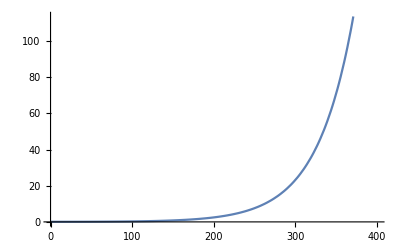

```mathematica
gexact=Plot[V[x],{x,a,b},DisplayFunction->Identity]
```

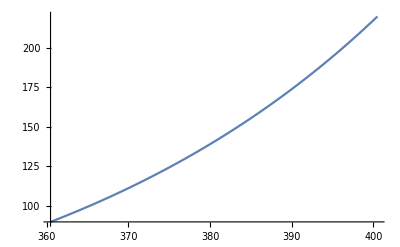

```mathematica
gexactbis=Plot[V[x],{x,9b/10,b},DisplayFunction->Identity]
```

### Definición del funcional asociado al caso R y G constantes

```mathematica
R[x_]:=r
G[x_]:=g
```

```mathematica
G[x]
```

0.01

```mathematica
Clear[x,F,FF]
(* denotaremos  y≡y1, y'≡p1, y''≡p2 y así sucesivamente *)
F[x_,y1_,p1_]:=p1^2+R[x]G[x] y1^2
FF[y_]:=∫_a^b F[x,y,D[y, x]]ⅆx
```

```mathematica
FF[y[x]]
```

∫_0^400.5 (0.0005 y[x]^2+y'[x]^2)ⅆx

```mathematica
(* Veámos cuál es el valor del funcional en la solución exacta, si la hubiera *)
valexactofunc=FF[V[x]]
```

1082.26

### Introducción de los extremos del intervalo y las condiciones de contorno de tipo Dirichlet de nuestro problema

```mathematica
a=y0;b=y4;
yb=VL; yL = yb
```

220

### Construcción de la partición del intervalo

Introducimos el número total de subintervalos, de igual longitud, en los que se subdivide el intervalo [a,b]. Pero en este caso concreto ya que sabemos que la solución debe ser una línea recta. Por tanto,  bastará con tomar el propio intervalo sin subdividir para obtener la solución exacta, como veremos más adelante.

```mathematica
n=100
```

100

Y posteriormente se definen los nodos de la correspondiente partición uniforme del intervalo.

```mathematica
Clear[x,y,h]
h=(b-a)/n;
x[i_]:=a+i h
```

Y se implementan en los nodos extremos las condiciones de contorno de tipo Dirichlet introducidas previamente.

```mathematica
n
```

100

```mathematica
y[n]=yb;
```

### Cálculo de la función de varias variables que se va a optimizar y de sus puntos críticos

```mathematica
F[x,y,p]
```

p^2+0.0005 y^2

```mathematica
x[1]
```

4.005

```mathematica
F[x,y,p]
```

p^2+0.0005 y^2

```mathematica
i=1;Expand[F[x,y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]-((y[i]-y[i-1])/h)^2-0.0005(y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h)^2]
```

0.

```mathematica
integrando =Expand[0.0005(y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h)^2+((y[i]-y[i-1])/h)^2]
```

0.+0.062844 y[0]^2-0.000249688 x y[0]^2+0.000031172 x^2 y[0]^2-0.124688 y[0] y[1]+0.000249688 x y[0] y[1]-0.000062344 x^2 y[0] y[1]+0.062344 y[1]^2+0.000031172 x^2 y[1]^2

```mathematica
F[x,y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]//Expand
```

0.+0.062844 y[0]^2-0.000249688 x y[0]^2+0.000031172 x^2 y[0]^2-0.124688 y[0] y[1]+0.000249688 x y[0] y[1]-0.000062344 x^2 y[0] y[1]+0.062344 y[1]^2+0.000031172 x^2 y[1]^2

```mathematica
Factor[∫_x[i-1]^x[i] integrandoⅆx]
```

0.250355 (1. y[0]^2-1.992 y[0] y[1]+1. y[1]^2)

```mathematica
Factor[∫_x[i-1]^x[i] Expand[F[x,y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]]ⅆx]
```

0.250355 (1. y[0]^2-1.992 y[0] y[1]+1. y[1]^2)

```mathematica
Factor[∫_x[i-1]^x[i] F[z,y[i-1]+((z-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]ⅆz]
```

(0.250355 (1. y[0]^3-2.992 y[0]^2 y[1]+2.992 y[0] y[1]^2-1. y[1]^3))/(1. y[0]-1. y[1])

```mathematica
∫_x[i-1]^x[i] F[x,y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]ⅆx
```

0.+0.249688 y[0]^2+(0.0006675 y[0]^3)/(1. y[0]-1. y[1])-0.499376 y[0] y[1]+0.249688 y[1]^2-(0.0006675 y[1]^3)/(1. y[0]-1. y[1])

```mathematica
Clear[GG]
GG=Simplify[∑_(i=1)^n 
∫_x[i-1]^x[i] Expand[F[x,y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]]ⅆx]
```

12117.2+0.250355 y[0]^2-0.498708 y[0] y[1]+0.500711 y[1]^2-0.498708 y[1] y[2]+0.500711 y[2]^2-0.498708 y[2] y[3]+0.500711 y[3]^2-0.498708 y[3] y[4]+0.500711 y[4]^2-0.498708 y[4] y[5]+0.500711 y[5]^2-0.498708 y[5] y[6]+0.500711 y[6]^2-0.498708 y[6] y[7]+0.500711 y[7]^2-0.498708 y[7] y[8]+0.500711 y[8]^2-0.498708 y[8] y[9]+0.500711 y[9]^2-0.498708 y[9] y[10]+0.500711 y[10]^2-0.498708 y[10] y[11]+0.500711 y[11]^2-0.498708 y[11] y[12]+0.500711 y[12]^2-0.498708 y[12] y[13]+0.500711 y[13]^2-0.498708 y[13] y[14]+0.500711 y[14]^2-0.498708 y[14] y[15]+0.500711 y[15]^2-0.498708 y[15] y[16]+0.500711 y[16]^2-0.498708 y[16] y[17]+0.500711 y[17]^2-0.498708 y[17] y[18]+0.500711 y[18]^2-0.498708 y[18] y[19]+0.500711 y[19]^2-0.498708 y[19] y[20]+0.500711 y[20]^2-0.498708 y[20] y[21]+0.500711 y[21]^2-0.498708 y[21] y[22]+0.500711 y[22]^2-0.498708 y[22] y[23]+0.500711 y[23]^2-0.498708 y[23] y[24]+0.500711 y[24]^2-0.498708 y[24] y[25]+0.500711 y[25]^2-0.498708 y[25] y[26]+0.500711 y[26]^2-0.498708 y[26] y[27]+0.500711 y[27]^2-0.498708 y[27] y[28]+0.500711 y[28]^2-0.498708 y[28] y[29]+0.500711 y[29]^2-0.498708 y[29] y[30]+0.500711 y[30]^2-0.498708 y[30] y[31]+0.500711 y[31]^2-0.498708 y[31] y[32]+0.500711 y[32]^2-0.498708 y[32] y[33]+0.500711 y[33]^2-0.498708 y[33] y[34]+0.500711 y[34]^2-0.498708 y[34] y[35]+0.500711 y[35]^2-0.498708 y[35] y[36]+0.500711 y[36]^2-0.498708 y[36] y[37]+0.500711 y[37]^2-0.498708 y[37] y[38]+0.500711 y[38]^2-0.498708 y[38] y[39]+0.500711 y[39]^2-0.498708 y[39] y[40]+0.500711 y[40]^2-0.498708 y[40] y[41]+0.500711 y[41]^2-0.498708 y[41] y[42]+0.500711 y[42]^2-0.498708 y[42] y[43]+0.500711 y[43]^2-0.498708 y[43] y[44]+0.500711 y[44]^2-0.498708 y[44] y[45]+0.500711 y[45]^2-0.498708 y[45] y[46]+0.500711 y[46]^2-0.498708 y[46] y[47]+0.500711 y[47]^2-0.498708 y[47] y[48]+0.500711 y[48]^2-0.498708 y[48] y[49]+0.500711 y[49]^2-0.498708 y[49] y[50]+0.500711 y[50]^2-0.498708 y[50] y[51]+0.500711 y[51]^2-0.498708 y[51] y[52]+0.500711 y[52]^2-0.498708 y[52] y[53]+0.500711 y[53]^2-0.498708 y[53] y[54]+0.500711 y[54]^2-0.498708 y[54] y[55]+0.500711 y[55]^2-0.498708 y[55] y[56]+0.500711 y[56]^2-0.498708 y[56] y[57]+0.500711 y[57]^2-0.498708 y[57] y[58]+0.500711 y[58]^2-0.498708 y[58] y[59]+0.500711 y[59]^2-0.498708 y[59] y[60]+0.500711 y[60]^2-0.498708 y[60] y[61]+0.500711 y[61]^2-0.498708 y[61] y[62]+0.500711 y[62]^2-0.498708 y[62] y[63]+0.500711 y[63]^2-0.498708 y[63] y[64]+0.500711 y[64]^2-0.498708 y[64] y[65]+0.500711 y[65]^2-0.498708 y[65] y[66]+0.500711 y[66]^2-0.498708 y[66] y[67]+0.500711 y[67]^2-0.498708 y[67] y[68]+0.500711 y[68]^2-0.498708 y[68] y[69]+0.500711 y[69]^2-0.498708 y[69] y[70]+0.500711 y[70]^2-0.498708 y[70] y[71]+0.500711 y[71]^2-0.498708 y[71] y[72]+0.500711 y[72]^2-0.498708 y[72] y[73]+0.500711 y[73]^2-0.498708 y[73] y[74]+0.500711 y[74]^2-0.498708 y[74] y[75]+0.500711 y[75]^2-0.498708 y[75] y[76]+0.500711 y[76]^2-0.498708 y[76] y[77]+0.500711 y[77]^2-0.498708 y[77] y[78]+0.500711 y[78]^2-0.498708 y[78] y[79]+0.500711 y[79]^2-0.498708 y[79] y[80]+0.500711 y[80]^2-0.498708 y[80] y[81]+0.500711 y[81]^2-0.498708 y[81] y[82]+0.500711 y[82]^2-0.498708 y[82] y[83]+0.500711 y[83]^2-0.498708 y[83] y[84]+0.500711 y[84]^2-0.498708 y[84] y[85]+0.500711 y[85]^2-0.498708 y[85] y[86]+0.500711 y[86]^2-0.498708 y[86] y[87]+0.500711 y[87]^2-0.498708 y[87] y[88]+0.500711 y[88]^2-0.498708 y[88] y[89]+0.500711 y[89]^2-0.498708 y[89] y[90]+0.500711 y[90]^2-0.498708 y[90] y[91]+0.500711 y[91]^2-0.498708 y[91] y[92]+0.500711 y[92]^2-0.498708 y[92] y[93]+0.500711 y[93]^2-0.498708 y[93] y[94]+0.500711 y[94]^2-0.498708 y[94] y[95]+0.500711 y[95]^2-0.498708 y[95] y[96]+0.500711 y[96]^2-0.498708 y[96] y[97]+0.500711 y[97]^2-0.498708 y[97] y[98]+0.500711 y[98]^2-109.716 y[99]-0.498708 y[98] y[99]+0.500711 y[99]^2

```mathematica
ptoscrit1=Chop[NSolve[Table[D[GG, y[i]]==0,{i,0,n-1}],Table[y[i],{i,0,n-1}]]]
```

{{y[0]→0.0566042,y[1]→0.0568314,y[2]→0.0575151,y[3]→0.0586607,y[4]→0.0602774,y[5]→0.0623781,y[6]→0.0649798,y[7]→0.0681033,y[8]→0.0717737,y[9]→0.0760206,y[10]→0.0808779,y[11]→0.0863847,y[12]→0.0925853,y[13]→0.0995294,y[14]→0.107273,y[15]→0.115878,y[16]→0.125413,y[17]→0.135956,y[18]→0.14759,y[19]→0.16041,y[20]→0.174518,y[21]→0.190027,y[22]→0.207063,y[23]→0.225761,y[24]→0.246273,y[25]→0.268762,y[26]→0.293409,y[27]→0.320413,y[28]→0.34999,y[29]→0.382378,y[30]→0.417836,y[31]→0.45665,y[32]→0.499131,y[33]→0.545621,y[34]→0.596492,y[35]→0.652154,y[36]→0.713053,y[37]→0.779678,y[38]→0.852565,y[39]→0.932298,y[40]→1.01952,y[41]→1.11493,y[42]→1.21929,y[43]→1.33344,y[44]→1.4583,y[45]→1.59488,y[46]→1.74426,y[47]→1.90765,y[48]→2.08636,y[49]→2.28182,y[50]→2.49561,y[51]→2.72944,y[52]→2.98519,y[53]→3.26491,y[54]→3.57085,y[55]→3.90547,y[56]→4.27145,y[57]→4.67174,y[58]→5.10954,y[59]→5.58838,y[60]→6.1121,y[61]→6.6849,y[62]→7.31138,y[63]→7.99658,y[64]→8.746,y[65]→9.56566,y[66]→10.4621,y[67]→11.4426,y[68]→12.515,y[69]→13.6879,y[70]→14.9707,y[71]→16.3738,y[72]→17.9083,y[73]→19.5867,y[74]→21.4223,y[75]→23.43,y[76]→25.6258,y[77]→28.0275,y[78]→30.6542,y[79]→33.5271,y[80]→36.6693,y[81]→40.1059,y[82]→43.8646,y[83]→47.9756,y[84]→52.4718,y[85]→57.3895,y[86]→62.768,y[87]→68.6506,y[88]→75.0845,y[89]→82.1214,y[90]→89.8178,y[91]→98.2355,y[92]→107.442,y[93]→117.512,y[94]→128.525,y[95]→140.57,y[96]→153.744,y[97]→168.153,y[98]→183.912,y[99]→201.148}}

```mathematica
yy1=Table[y[i],{i,0,n}]/.ptoscrit1⟦1⟧
```

{0.0566042,0.0568314,0.0575151,0.0586607,0.0602774,0.0623781,0.0649798,0.0681033,0.0717737,0.0760206,0.0808779,0.0863847,0.0925853,0.0995294,0.107273,0.115878,0.125413,0.135956,0.14759,0.16041,0.174518,0.190027,0.207063,0.225761,0.246273,0.268762,0.293409,0.320413,0.34999,0.382378,0.417836,0.45665,0.499131,0.545621,0.596492,0.652154,0.713053,0.779678,0.852565,0.932298,1.01952,1.11493,1.21929,1.33344,1.4583,1.59488,1.74426,1.90765,2.08636,2.28182,2.49561,2.72944,2.98519,3.26491,3.57085,3.90547,4.27145,4.67174,5.10954,5.58838,6.1121,6.6849,7.31138,7.99658,8.746,9.56566,10.4621,11.4426,12.515,13.6879,14.9707,16.3738,17.9083,19.5867,21.4223,23.43,25.6258,28.0275,30.6542,33.5271,36.6693,40.1059,43.8646,47.9756,52.4718,57.3895,62.768,68.6506,75.0845,82.1214,89.8178,98.2355,107.442,117.512,128.525,140.57,153.744,168.153,183.912,201.148,220}

### Construcción de la poligonal correspondiente

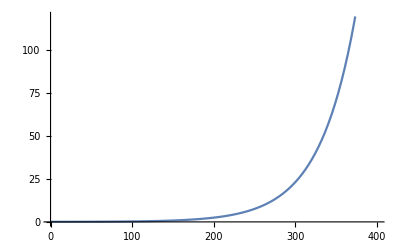

```mathematica
yy1=Table[y[i],{i,0,n}]/.ptoscrit1⟦1⟧;
gg1=ListPlot[Table[{x[i],yy1⟦i+1⟧},{i,0,n}],PlotJoined->True,DisplayFunction->Identity]
```

### Valor aproximado del extremo del funcional

```mathematica
GG/.ptoscrit1⟦1⟧
```

1082.62

```mathematica
valexactofunc
```

1082.26

### Evaluación aproximada de la integral

Puede resultar muy conveniente usar una regla de cuadratura apropiada para evaluar mucho más fácilmente las integrales de la fórmula anterior. En este caso hemos implementado la conocida regla de los trapecios, obteniendo -como veremos- valores muy aceptables, con un esfuerzo computacional pequeño.

```mathematica
Clear[GGG]
GGG=∑_(i=1)^n 1/2 h (F[x[i-1],y[i-1],(y[i]-y[i-1])/h]+F[x[i],y[i],(y[i]-y[i-1])/h])
```

2.0025 (0.0005 y[0]^2+0.0005 y[1]^2+0.124688 (-y[0]+y[1])^2)+2.0025 (0.0005 y[1]^2+0.0005 y[2]^2+0.124688 (-y[1]+y[2])^2)+2.0025 (0.0005 y[2]^2+0.0005 y[3]^2+0.124688 (-y[2]+y[3])^2)+2.0025 (0.0005 y[3]^2+0.0005 y[4]^2+0.124688 (-y[3]+y[4])^2)+2.0025 (0.0005 y[4]^2+0.0005 y[5]^2+0.124688 (-y[4]+y[5])^2)+2.0025 (0.0005 y[5]^2+0.0005 y[6]^2+0.124688 (-y[5]+y[6])^2)+2.0025 (0.0005 y[6]^2+0.0005 y[7]^2+0.124688 (-y[6]+y[7])^2)+2.0025 (0.0005 y[7]^2+0.0005 y[8]^2+0.124688 (-y[7]+y[8])^2)+2.0025 (0.0005 y[8]^2+0.0005 y[9]^2+0.124688 (-y[8]+y[9])^2)+2.0025 (0.0005 y[9]^2+0.0005 y[10]^2+0.124688 (-y[9]+y[10])^2)+2.0025 (0.0005 y[10]^2+0.0005 y[11]^2+0.124688 (-y[10]+y[11])^2)+2.0025 (0.0005 y[11]^2+0.0005 y[12]^2+0.124688 (-y[11]+y[12])^2)+2.0025 (0.0005 y[12]^2+0.0005 y[13]^2+0.124688 (-y[12]+y[13])^2)+2.0025 (0.0005 y[13]^2+0.0005 y[14]^2+0.124688 (-y[13]+y[14])^2)+2.0025 (0.0005 y[14]^2+0.0005 y[15]^2+0.124688 (-y[14]+y[15])^2)+2.0025 (0.0005 y[15]^2+0.0005 y[16]^2+0.124688 (-y[15]+y[16])^2)+2.0025 (0.0005 y[16]^2+0.0005 y[17]^2+0.124688 (-y[16]+y[17])^2)+2.0025 (0.0005 y[17]^2+0.0005 y[18]^2+0.124688 (-y[17]+y[18])^2)+2.0025 (0.0005 y[18]^2+0.0005 y[19]^2+0.124688 (-y[18]+y[19])^2)+2.0025 (0.0005 y[19]^2+0.0005 y[20]^2+0.124688 (-y[19]+y[20])^2)+2.0025 (0.0005 y[20]^2+0.0005 y[21]^2+0.124688 (-y[20]+y[21])^2)+2.0025 (0.0005 y[21]^2+0.0005 y[22]^2+0.124688 (-y[21]+y[22])^2)+2.0025 (0.0005 y[22]^2+0.0005 y[23]^2+0.124688 (-y[22]+y[23])^2)+2.0025 (0.0005 y[23]^2+0.0005 y[24]^2+0.124688 (-y[23]+y[24])^2)+2.0025 (0.0005 y[24]^2+0.0005 y[25]^2+0.124688 (-y[24]+y[25])^2)+2.0025 (0.0005 y[25]^2+0.0005 y[26]^2+0.124688 (-y[25]+y[26])^2)+2.0025 (0.0005 y[26]^2+0.0005 y[27]^2+0.124688 (-y[26]+y[27])^2)+2.0025 (0.0005 y[27]^2+0.0005 y[28]^2+0.124688 (-y[27]+y[28])^2)+2.0025 (0.0005 y[28]^2+0.0005 y[29]^2+0.124688 (-y[28]+y[29])^2)+2.0025 (0.0005 y[29]^2+0.0005 y[30]^2+0.124688 (-y[29]+y[30])^2)+2.0025 (0.0005 y[30]^2+0.0005 y[31]^2+0.124688 (-y[30]+y[31])^2)+2.0025 (0.0005 y[31]^2+0.0005 y[32]^2+0.124688 (-y[31]+y[32])^2)+2.0025 (0.0005 y[32]^2+0.0005 y[33]^2+0.124688 (-y[32]+y[33])^2)+2.0025 (0.0005 y[33]^2+0.0005 y[34]^2+0.124688 (-y[33]+y[34])^2)+2.0025 (0.0005 y[34]^2+0.0005 y[35]^2+0.124688 (-y[34]+y[35])^2)+2.0025 (0.0005 y[35]^2+0.0005 y[36]^2+0.124688 (-y[35]+y[36])^2)+2.0025 (0.0005 y[36]^2+0.0005 y[37]^2+0.124688 (-y[36]+y[37])^2)+2.0025 (0.0005 y[37]^2+0.0005 y[38]^2+0.124688 (-y[37]+y[38])^2)+2.0025 (0.0005 y[38]^2+0.0005 y[39]^2+0.124688 (-y[38]+y[39])^2)+2.0025 (0.0005 y[39]^2+0.0005 y[40]^2+0.124688 (-y[39]+y[40])^2)+2.0025 (0.0005 y[40]^2+0.0005 y[41]^2+0.124688 (-y[40]+y[41])^2)+2.0025 (0.0005 y[41]^2+0.0005 y[42]^2+0.124688 (-y[41]+y[42])^2)+2.0025 (0.0005 y[42]^2+0.0005 y[43]^2+0.124688 (-y[42]+y[43])^2)+2.0025 (0.0005 y[43]^2+0.0005 y[44]^2+0.124688 (-y[43]+y[44])^2)+2.0025 (0.0005 y[44]^2+0.0005 y[45]^2+0.124688 (-y[44]+y[45])^2)+2.0025 (0.0005 y[45]^2+0.0005 y[46]^2+0.124688 (-y[45]+y[46])^2)+2.0025 (0.0005 y[46]^2+0.0005 y[47]^2+0.124688 (-y[46]+y[47])^2)+2.0025 (0.0005 y[47]^2+0.0005 y[48]^2+0.124688 (-y[47]+y[48])^2)+2.0025 (0.0005 y[48]^2+0.0005 y[49]^2+0.124688 (-y[48]+y[49])^2)+2.0025 (0.0005 y[49]^2+0.0005 y[50]^2+0.124688 (-y[49]+y[50])^2)+2.0025 (0.0005 y[50]^2+0.0005 y[51]^2+0.124688 (-y[50]+y[51])^2)+2.0025 (0.0005 y[51]^2+0.0005 y[52]^2+0.124688 (-y[51]+y[52])^2)+2.0025 (0.0005 y[52]^2+0.0005 y[53]^2+0.124688 (-y[52]+y[53])^2)+2.0025 (0.0005 y[53]^2+0.0005 y[54]^2+0.124688 (-y[53]+y[54])^2)+2.0025 (0.0005 y[54]^2+0.0005 y[55]^2+0.124688 (-y[54]+y[55])^2)+2.0025 (0.0005 y[55]^2+0.0005 y[56]^2+0.124688 (-y[55]+y[56])^2)+2.0025 (0.0005 y[56]^2+0.0005 y[57]^2+0.124688 (-y[56]+y[57])^2)+2.0025 (0.0005 y[57]^2+0.0005 y[58]^2+0.124688 (-y[57]+y[58])^2)+2.0025 (0.0005 y[58]^2+0.0005 y[59]^2+0.124688 (-y[58]+y[59])^2)+2.0025 (0.0005 y[59]^2+0.0005 y[60]^2+0.124688 (-y[59]+y[60])^2)+2.0025 (0.0005 y[60]^2+0.0005 y[61]^2+0.124688 (-y[60]+y[61])^2)+2.0025 (0.0005 y[61]^2+0.0005 y[62]^2+0.124688 (-y[61]+y[62])^2)+2.0025 (0.0005 y[62]^2+0.0005 y[63]^2+0.124688 (-y[62]+y[63])^2)+2.0025 (0.0005 y[63]^2+0.0005 y[64]^2+0.124688 (-y[63]+y[64])^2)+2.0025 (0.0005 y[64]^2+0.0005 y[65]^2+0.124688 (-y[64]+y[65])^2)+2.0025 (0.0005 y[65]^2+0.0005 y[66]^2+0.124688 (-y[65]+y[66])^2)+2.0025 (0.0005 y[66]^2+0.0005 y[67]^2+0.124688 (-y[66]+y[67])^2)+2.0025 (0.0005 y[67]^2+0.0005 y[68]^2+0.124688 (-y[67]+y[68])^2)+2.0025 (0.0005 y[68]^2+0.0005 y[69]^2+0.124688 (-y[68]+y[69])^2)+2.0025 (0.0005 y[69]^2+0.0005 y[70]^2+0.124688 (-y[69]+y[70])^2)+2.0025 (0.0005 y[70]^2+0.0005 y[71]^2+0.124688 (-y[70]+y[71])^2)+2.0025 (0.0005 y[71]^2+0.0005 y[72]^2+0.124688 (-y[71]+y[72])^2)+2.0025 (0.0005 y[72]^2+0.0005 y[73]^2+0.124688 (-y[72]+y[73])^2)+2.0025 (0.0005 y[73]^2+0.0005 y[74]^2+0.124688 (-y[73]+y[74])^2)+2.0025 (0.0005 y[74]^2+0.0005 y[75]^2+0.124688 (-y[74]+y[75])^2)+2.0025 (0.0005 y[75]^2+0.0005 y[76]^2+0.124688 (-y[75]+y[76])^2)+2.0025 (0.0005 y[76]^2+0.0005 y[77]^2+0.124688 (-y[76]+y[77])^2)+2.0025 (0.0005 y[77]^2+0.0005 y[78]^2+0.124688 (-y[77]+y[78])^2)+2.0025 (0.0005 y[78]^2+0.0005 y[79]^2+0.124688 (-y[78]+y[79])^2)+2.0025 (0.0005 y[79]^2+0.0005 y[80]^2+0.124688 (-y[79]+y[80])^2)+2.0025 (0.0005 y[80]^2+0.0005 y[81]^2+0.124688 (-y[80]+y[81])^2)+2.0025 (0.0005 y[81]^2+0.0005 y[82]^2+0.124688 (-y[81]+y[82])^2)+2.0025 (0.0005 y[82]^2+0.0005 y[83]^2+0.124688 (-y[82]+y[83])^2)+2.0025 (0.0005 y[83]^2+0.0005 y[84]^2+0.124688 (-y[83]+y[84])^2)+2.0025 (0.0005 y[84]^2+0.0005 y[85]^2+0.124688 (-y[84]+y[85])^2)+2.0025 (0.0005 y[85]^2+0.0005 y[86]^2+0.124688 (-y[85]+y[86])^2)+2.0025 (0.0005 y[86]^2+0.0005 y[87]^2+0.124688 (-y[86]+y[87])^2)+2.0025 (0.0005 y[87]^2+0.0005 y[88]^2+0.124688 (-y[87]+y[88])^2)+2.0025 (0.0005 y[88]^2+0.0005 y[89]^2+0.124688 (-y[88]+y[89])^2)+2.0025 (0.0005 y[89]^2+0.0005 y[90]^2+0.124688 (-y[89]+y[90])^2)+2.0025 (0.0005 y[90]^2+0.0005 y[91]^2+0.124688 (-y[90]+y[91])^2)+2.0025 (0.0005 y[91]^2+0.0005 y[92]^2+0.124688 (-y[91]+y[92])^2)+2.0025 (0.0005 y[92]^2+0.0005 y[93]^2+0.124688 (-y[92]+y[93])^2)+2.0025 (0.0005 y[93]^2+0.0005 y[94]^2+0.124688 (-y[93]+y[94])^2)+2.0025 (0.0005 y[94]^2+0.0005 y[95]^2+0.124688 (-y[94]+y[95])^2)+2.0025 (0.0005 y[95]^2+0.0005 y[96]^2+0.124688 (-y[95]+y[96])^2)+2.0025 (0.0005 y[96]^2+0.0005 y[97]^2+0.124688 (-y[96]+y[97])^2)+2.0025 (0.0005 y[97]^2+0.0005 y[98]^2+0.124688 (-y[97]+y[98])^2)+2.0025 (24.2+0.124688 (220-y[99])^2+0.0005 y[99]^2)+2.0025 (0.0005 y[98]^2+0.0005 y[99]^2+0.124688 (-y[98]+y[99])^2)

```mathematica
ptoscrit2=NSolve[Table[D[GGG, y[i]]==0,{i,0,n-1}],Table[y[i],{i,0,n-1}]]
```

{{y[0]→0.056944,y[1]→0.0571723,y[2]→0.0578592,y[3]→0.0590101,y[4]→0.0606342,y[5]→0.0627447,y[6]→0.0653583,y[7]→0.0684962,y[8]→0.0721834,y[9]→0.0764494,y[10]→0.0813287,y[11]→0.0868601,y[12]→0.0930882,y[13]→0.100063,y[14]→0.10784,y[15]→0.116482,y[16]→0.126058,y[17]→0.136646,y[18]→0.148329,y[19]→0.161201,y[20]→0.175367,y[21]→0.190939,y[22]→0.208042,y[23]→0.226814,y[24]→0.247405,y[25]→0.26998,y[26]→0.29472,y[27]→0.321824,y[28]→0.351509,y[29]→0.384013,y[30]→0.419597,y[31]→0.458546,y[32]→0.501173,y[33]→0.547819,y[34]→0.598859,y[35]→0.654701,y[36]→0.715794,y[37]→0.782628,y[38]→0.855739,y[39]→0.935712,y[40]→1.02319,y[41]→1.11887,y[42]→1.22353,y[43]→1.338,y[44]→1.4632,y[45]→1.60014,y[46]→1.74991,y[47]→1.91371,y[48]→2.09286,y[49]→2.2888,y[50]→2.50309,y[51]→2.73746,y[52]→2.99378,y[53]→3.27411,y[54]→3.5807,y[55]→3.91601,y[56]→4.28272,y[57]→4.68378,y[58]→5.12241,y[59]→5.60211,y[60]→6.12675,y[61]→6.70052,y[62]→7.32803,y[63]→8.01431,y[64]→8.76487,y[65]→9.58572,y[66]→10.4834,y[67]→11.4653,y[68]→12.539,y[69]→13.7133,y[70]→14.9976,y[71]→16.4022,y[72]→17.9383,y[73]→19.6183,y[74]→21.4557,y[75]→23.4651,y[76]→25.6627,y[77]→28.0661,y[78]→30.6946,y[79]→33.5693,y[80]→36.7132,y[81]→40.1515,y[82]→43.9119,y[83]→48.0244,y[84]→52.5221,y[85]→57.441,y[86]→62.8206,y[87]→68.704,y[88]→75.1384,y[89]→82.1755,y[90]→89.8715,y[91]→98.2884,y[92]→107.494,y[93]→117.561,y[94]→128.571,y[95]→140.612,y[96]→153.781,y[97]→168.183,y[98]→183.934,y[99]→201.16}}

{0.056944,0.0571723,0.0578592,0.0590101,0.0606342,0.0627447,0.0653583,0.0684962,0.0721834,0.0764494,0.0813287,0.0868601,0.0930882,0.100063,0.10784,0.116482,0.126058,0.136646,0.148329,0.161201,0.175367,0.190939,0.208042,0.226814,0.247405,0.26998,0.29472,0.321824,0.351509,0.384013,0.419597,0.458546,0.501173,0.547819,0.598859,0.654701,0.715794,0.782628,0.855739,0.935712,1.02319,1.11887,1.22353,1.338,1.4632,1.60014,1.74991,1.91371,2.09286,2.2888,2.50309,2.73746,2.99378,3.27411,3.5807,3.91601,4.28272,4.68378,5.12241,5.60211,6.12675,6.70052,7.32803,8.01431,8.76487,9.58572,10.4834,11.4653,12.539,13.7133,14.9976,16.4022,17.9383,19.6183,21.4557,23.4651,25.6627,28.0661,30.6946,33.5693,36.7132,40.1515,43.9119,48.0244,52.5221,57.441,62.8206,68.704,75.1384,82.1755,89.8715,98.2884,107.494,117.561,128.571,140.612,153.781,168.183,183.934,201.16,220}

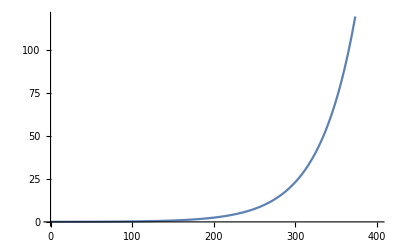

```mathematica
yy2=Table[y[i],{i,0,n}]/.ptoscrit2⟦1⟧
gg2=ListPlot[Table[{x[i],yy2⟦i+1⟧},{i,0,n}],PlotJoined->True,DisplayFunction->Identity]
```

```mathematica
N[GGG/.ptoscrit2⟦1⟧]
```

1083.34

```mathematica
valexactofunc
```

1082.26

### Comparación de los valores obtenidos para la solución exacta y las aproximaciones

```mathematica
TableForm[Table[{x[i],V[x[i]],yy1⟦i+1⟧,yy2⟦i+1⟧},{i,0,n}],
TableHeadings->{None,
{"x[i] \n","y[x[i]]  \n","y[i]  \n","y[i](trap.)\n"}}]
```

x[i] 
 | y[x[i]]  
 | y[i]  
 | y[i](trap.)

0. | 0.056774 | 0.0566042 | 0.056944
4.005 | 0.0570018 | 0.0568314 | 0.0571723
8.01 | 0.0576871 | 0.0575151 | 0.0578592
12.015 | 0.0588353 | 0.0586607 | 0.0590101
16.02 | 0.0604557 | 0.0602774 | 0.0606342
20.025 | 0.0625613 | 0.0623781 | 0.0627447
24.03 | 0.065169 | 0.0649798 | 0.0653583
28.035 | 0.0682996 | 0.0681033 | 0.0684962
32.04 | 0.0719784 | 0.0717737 | 0.0721834
36.045 | 0.0762349 | 0.0760206 | 0.0764494
40.05 | 0.0811032 | 0.0808779 | 0.0813287
44.055 | 0.0866223 | 0.0863847 | 0.0868601
48.06 | 0.0928367 | 0.0925853 | 0.0930882
52.065 | 0.099796 | 0.0995294 | 0.100063
56.07 | 0.107556 | 0.107273 | 0.10784
60.075 | 0.11618 | 0.115878 | 0.116482
64.08 | 0.125736 | 0.125413 | 0.126058
68.085 | 0.136301 | 0.135956 | 0.136646
72.09 | 0.147959 | 0.14759 | 0.148329
76.095 | 0.160806 | 0.16041 | 0.161201
80.1 | 0.174942 | 0.174518 | 0.175367
84.105 | 0.190483 | 0.190027 | 0.190939
88.11 | 0.207552 | 0.207063 | 0.208042
92.115 | 0.226288 | 0.225761 | 0.226814
96.12 | 0.246839 | 0.246273 | 0.247405
100.125 | 0.269371 | 0.268762 | 0.26998
104.13 | 0.294065 | 0.293409 | 0.29472
108.135 | 0.321119 | 0.320413 | 0.321824
112.14 | 0.35075 | 0.34999 | 0.351509
116.145 | 0.383195 | 0.382378 | 0.384013
120.15 | 0.418717 | 0.417836 | 0.419597
124.155 | 0.457598 | 0.45665 | 0.458546
128.16 | 0.500152 | 0.499131 | 0.501173
132.165 | 0.54672 | 0.545621 | 0.547819
136.17 | 0.597675 | 0.596492 | 0.598859
140.175 | 0.653427 | 0.652154 | 0.654701
144.18 | 0.714423 | 0.713053 | 0.715794
148.185 | 0.781153 | 0.779678 | 0.782628
152.19 | 0.854152 | 0.852565 | 0.855739
156.195 | 0.934005 | 0.932298 | 0.935712
160.2 | 1.02135 | 1.01952 | 1.02319
164.205 | 1.1169 | 1.11493 | 1.11887
168.21 | 1.22141 | 1.21929 | 1.22353
172.215 | 1.33572 | 1.33344 | 1.338
176.22 | 1.46075 | 1.4583 | 1.4632
180.225 | 1.59751 | 1.59488 | 1.60014
184.23 | 1.74708 | 1.74426 | 1.74991
188.235 | 1.91068 | 1.90765 | 1.91371
192.24 | 2.08961 | 2.08636 | 2.09286
196.245 | 2.28531 | 2.28182 | 2.2888
200.25 | 2.49935 | 2.49561 | 2.50309
204.255 | 2.73345 | 2.72944 | 2.73746
208.26 | 2.98948 | 2.98519 | 2.99378
212.265 | 3.26951 | 3.26491 | 3.27411
216.27 | 3.57578 | 3.57085 | 3.5807
220.275 | 3.91074 | 3.90547 | 3.91601
224.28 | 4.27709 | 4.27145 | 4.28272
228.285 | 4.67776 | 4.67174 | 4.68378
232.29 | 5.11598 | 5.10954 | 5.12241
236.295 | 5.59525 | 5.58838 | 5.60211
240.3 | 6.11943 | 6.1121 | 6.12675
244.305 | 6.69271 | 6.6849 | 6.70052
248.31 | 7.31971 | 7.31138 | 7.32803
252.315 | 8.00545 | 7.99658 | 8.01431
256.32 | 8.75544 | 8.746 | 8.76487
260.325 | 9.57569 | 9.56566 | 9.58572
264.33 | 10.4728 | 10.4621 | 10.4834
268.335 | 11.4539 | 11.4426 | 11.4653
272.34 | 12.527 | 12.515 | 12.539
276.345 | 13.7006 | 13.6879 | 13.7133
280.35 | 14.9842 | 14.9707 | 14.9976
284.355 | 16.388 | 16.3738 | 16.4022
288.36 | 17.9233 | 17.9083 | 17.9383
292.365 | 19.6025 | 19.5867 | 19.6183
296.37 | 21.439 | 21.4223 | 21.4557
300.375 | 23.4475 | 23.43 | 23.4651
304.38 | 25.6443 | 25.6258 | 25.6627
308.385 | 28.0468 | 28.0275 | 28.0661
312.39 | 30.6744 | 30.6542 | 30.6946
316.395 | 33.5482 | 33.5271 | 33.5693
320.4 | 36.6912 | 36.6693 | 36.7132
324.405 | 40.1287 | 40.1059 | 40.1515
328.41 | 43.8882 | 43.8646 | 43.9119
332.415 | 48. | 47.9756 | 48.0244
336.42 | 52.497 | 52.4718 | 52.5221
340.425 | 57.4152 | 57.3895 | 57.441
344.43 | 62.7943 | 62.768 | 62.8206
348.435 | 68.6773 | 68.6506 | 68.704
352.44 | 75.1115 | 75.0845 | 75.1384
356.445 | 82.1484 | 82.1214 | 82.1755
360.45 | 89.8447 | 89.8178 | 89.8715
364.455 | 98.262 | 98.2355 | 98.2884
368.46 | 107.468 | 107.442 | 107.494
372.465 | 117.536 | 117.512 | 117.561
376.47 | 128.548 | 128.525 | 128.571
380.475 | 140.591 | 140.57 | 140.612
384.48 | 153.763 | 153.744 | 153.781
388.485 | 168.168 | 168.153 | 168.183
392.49 | 183.923 | 183.912 | 183.934
396.495 | 201.154 | 201.148 | 201.16
400.5 | 220. | 220 | 220

#### Contraste gráfico

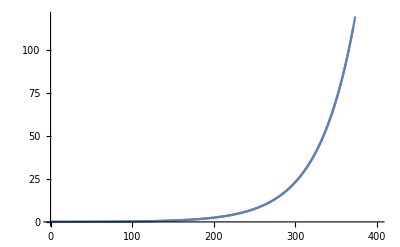

```mathematica
Show[gg1,gexact,DisplayFunction->$DisplayFunction]
```

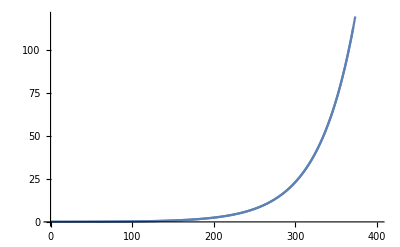

```mathematica
Show[gg2,gexact]
```

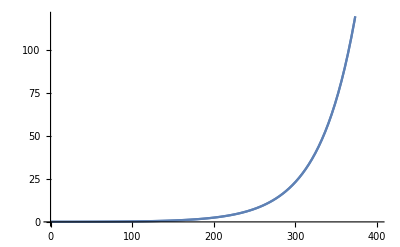

```mathematica
Show[gg1,gg2]
```

Comparamos en este gráfico las representaciones de la solución exacta, y la que proporcion el método de la poligonal de Euler, junto con la que se obtiene utilizando la regla de los trapecios para aproximar las integrales correspondientes.

## Relación con el elemento finito de Lagrange

Expondremos a continuación la idea subyacente en el conocido como elemento finito de Lagrange, que es el ejemplo más simple que se puede estudiar. En este elemento finito  se emplea sólamente el valor en ambos extremos del intervalo de la función que se quiere aproximar, obteniéndose así la simple interpolación de Lagrange de la misma mediante polinomios de grado 1. La idea consiste en utilizar este elemento finito para construir espacios de funciones aproximantes, según las particiones que tomemos del intervalo considerado, pegando trocitos de segmentos de recta, resultando así  funciones lineales a trozos pero que al menos son continuas. De esta manera volvemos a aproximar la verdadera solución del problema mediante una poligonal, como ocurría con la poligonal de Euler; resultando ambos métodos equivalentes cuando se aplican a problemas de contorno de segundo orden autoadjuntos.
El único problema, como sabemos, es que no podremos aplicar este método para aproximar directamente la ecuación de segundo orden de partida, ya que estas funciones poligonales no tienen la regularidad mínima requerida; no sólo no son de clase 2, sino que ni tan siquiera son de clase 1, ya que sólo lo son a trozos. Pero esto bastará para poder aplicarselo a la correspondiente formulación débil del problema de segundo orden de partida, ya que estas funciones splines lineales están incluidas en el espacio H^1(a,b)  de las funciones continuas con derivada continua a trozos y acotada (que es uno de los llamados espacios de Sobolev en dimensión uno que tanto se emplean cuando se habla de la formulación débil de distintos problemas variacionales y de contorno).

#### Base del elemento finito de Lagrange en un intervalo de referencia y afinidad a cualquier otro intervalo

Así pues, la idea del elemento finito de Lagrange, definido sobre un intervalo  de referencia, por ejemplo [0,1], consiste en obtener el único polinomio de grado 1, p(x)=c_0+c_1 x, que tome ciertos valores dados, α_1 y α_2, en los extremos de dicho intervalo. Es inmediato comprobar que dicho polinomio se expresa como

		p(x)=α_1 p_1(x)+α_2 p_2(x),
						
donde p_1(x)=1-x y p_2(x)=x (se cumple quep_1(0)=1, p_1(1)=0 y p_2(0)=0, p_2(1)=1).
Finalmente, si en vez de trabajar en el intervalo de referencia [0,1], tuviésemos  un intervalo cualquiera [a,b], bastaría con considerar la afinidad x→(x-a)/(b-a) entre ellos , escribiéndose el polinomio como

		p(x)=α_1 p_1((x-a)/(b-a))+α_2 p_2((x-a)/(b-a)).

Veamos todo esto, con un ejemplo en concreto. Para ello, empezaremos por definir los que se denominan polinomios de base de dicho elemento finito y que no son más que  p_1(x) y p_2(x).

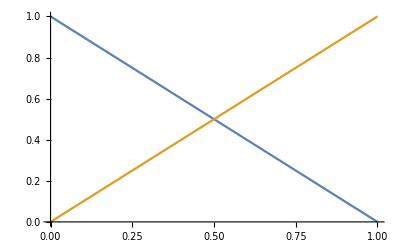

```mathematica
Subscript[p, 1][x_]:=1-x
Subscript[p, 2][x_]:=x
Plot[{Subscript[p, 1][x], Subscript[p, 2][x]},{x,0,1}]
```

Ahora si queremos obtener, por ejemplo la solución obtenida en el problema resuelto mediante el método de la poligonal de Euler en el que calculábamos la recta que pasa por los puntos (a,y_a) y (b,y_b), nos bastará emplear el correspondiente operador de interpolación lagrangiana:

```mathematica
ya =y[0]/.ptoscrit1[[1]]
```

0.0548987

```mathematica
ya Subscript[p, 1][(x-a)/(b-a)]+yb Subscript[p, 2][(x-a)/(b-a)]//Simplify
```

0.0548987+0.549176 x

No es más que la ecuación de la recta que pasa por los puntos (a,y_a) y (b,y_b), como comprobamos fácilmente:

```mathematica
ya Subscript[p, 1][(x-a)/(b-a)]+yb Subscript[p, 2][(x-a)/(b-a)]==(x-a)(yb-ya)/(b-a)+ya//Simplify
```

True

#### Discretización por elementos finitos

Sean  S_1(x_0,…,x_n) el espacio de funciones splines lineales continuas en el intervalo [a,b] y ^0 S_1(x_0,…,x_n) de aquellas que se anulan  en los puntos de la frontera. Entonces, una base de  ^0 S_1(x_0,…,x_n) es el conjunto {w_1,...,w_(n-1)} de funciones lineales a trozos tales que w_i(x_j)=1 si i=j y w_i(x_j)=0 si i≠j, que definimos a continuación:

```mathematica
Clear[i,t,w]
w[i_][t_]:=Which[x[i-1]≤t≤x[i], Subscript[p, 2][(t-x[i-1])/(x[i]-x[i-1])] ,x[i]≤t≤x[i+1], Subscript[p, 1][(t-x[i])/(x[i+1]-x[i])],True,0]
w[0][t_]:=Which[x[0]≤t≤x[1], Subscript[p, 1][(t-x[0])/(x[1]-x[0])] ,True,0]
w[n][t_]:=Which[x[n-1]≤t≤x[n], Subscript[p, 2][(t-x[n-1])/(x[n]-x[n-1])] ,True,0]
```

Las gráficas de estas funciones se muestran a continuación.

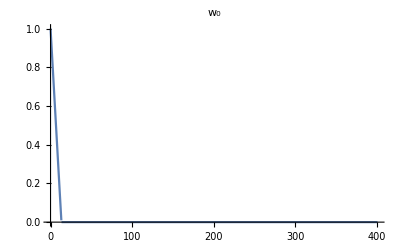

```mathematica
Plot[ w[0][t],{t,a,b},PlotRange->{0,1},(* AspectRatio->Automatic,*)PlotLabel->"w_0" ]
```

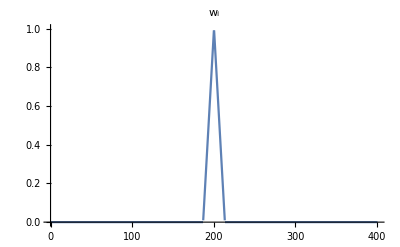

```mathematica
Plot[ w[n/2][t],{t,a,b},PlotRange->{0,1},(* AspectRatio->Automatic,*)PlotLabel->"w_i"]
```

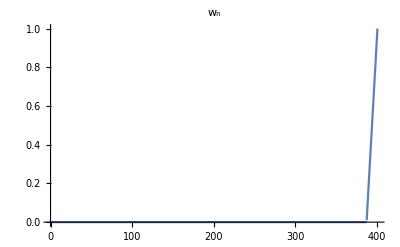

```mathematica
Plot[w[n][t],{t,a,b},PlotRange->{0,1},(* AspectRatio->Automatic,*)PlotLabel->"w_n"]
```

#### Construcción del correspondiente spline lineal a partir de la base del espacio de elementos finitos

La idea es que cualquier spline lineal puede obtenerse mediante la correspondiente combinación lineal de estas funciones de base, lineales a trozos.

```mathematica
Clear[c,zm]
ȳ[t_]:=(ya w[0][t]+∑_(i=1)^(n-1) y[i]  w[i][t]+yb w[n][t])/.ptoscrit1[[1]]
```

De manera que al evaluar esta función en cada uno de los nodos de la partición considerada  obtendremos el correspondiente valor asignado. Vamos a probar, con algunos nodos concretos.

```mathematica
ȳ[t]/.t->x[0]
```

0.0548987

```mathematica
ȳ[t]/.t->x[4]
```

0.0992816

```mathematica
ȳ[t]/.t->x[n]
```

220.

Vemos así que el método de la poligonal de Euler no es más que la aplicación del conocido como método de Ritz al funcional que se quiere optimizar, empleando como funciones "coordenadas" precisamente estas funciones lineales a trozos que se toman como funciones de base para los splines lineales de clase C^0.

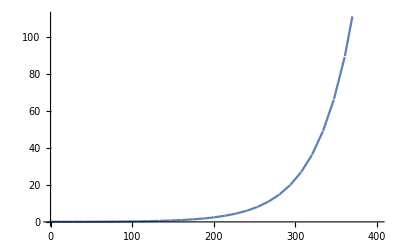

```mathematica
Plot[ȳ[t],{t,x[0],x[n]}]
```

## Ejemplo con R y G constantes con el funcional general

Resolveremos ahora otro problema de segundo orden, que proviene de la minimización del funcional energía correspondiente al caso en el que al menos R puede depender de la variable independiente, mientras que G, podría ser constante o no

		∂_x (1/(R(x))y'(x)) =  G(x) y(x), x∈[a,b]   (R(x) no supone que no se anula en todo caso)
		y’(a)=0 (cond. Neumann homogénea),  y(b)=y_b=V_L

 Habitualmente el intervalo en el que trabajaremos será [a,b]=[0,L].  Y podremos obtener también la solución de este problema de contorno como la única extremal del siguiente funcional energía asociado, que se puede ver que es estrictamente convexo y está definido como sigue

	L[y]=1/2∫_a^b (1/(R(x))y'(x)^2+G(x) (y(x))^2)dx       con y(b)=y_b (condición de tipo esencial que hay que imponer)
	
en un dominio de funciones, suficientemente regulares (ya sea de clase C^1, al menos a trozos y con derivada acotada, aunque no tenga porqué ser continua en todo el intervalo, como por ejemplo el espacio de los splines lineales de clase C^0, que además están incluidas en el correspondiente espacio más general en el que tiene sentido la definición del funcional, el denominado espacio de Sobolev H^1(a,b))

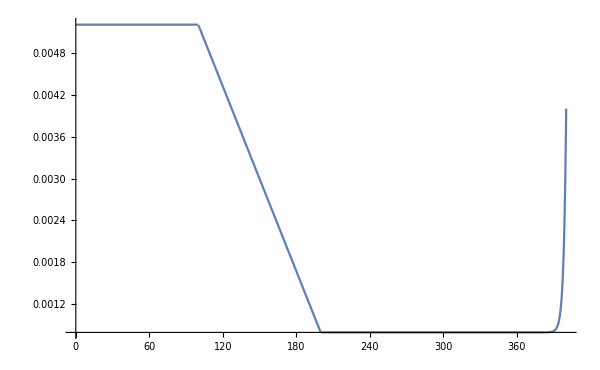
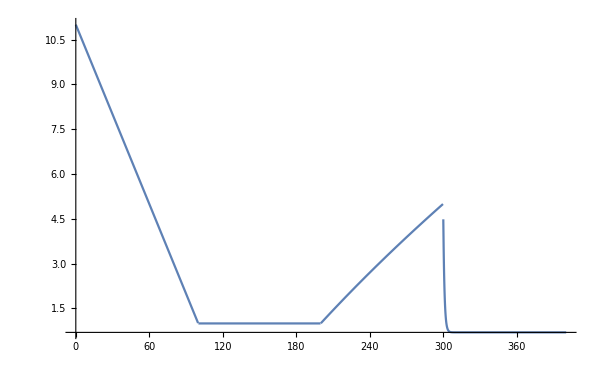
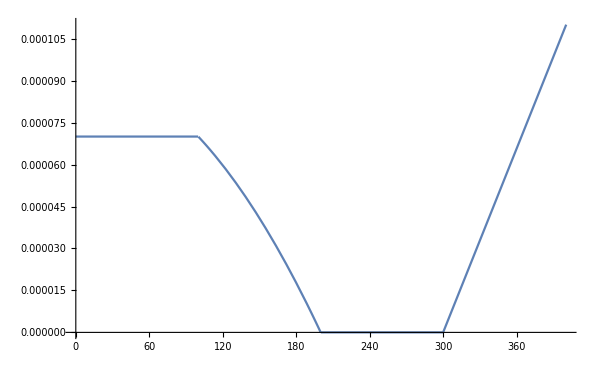
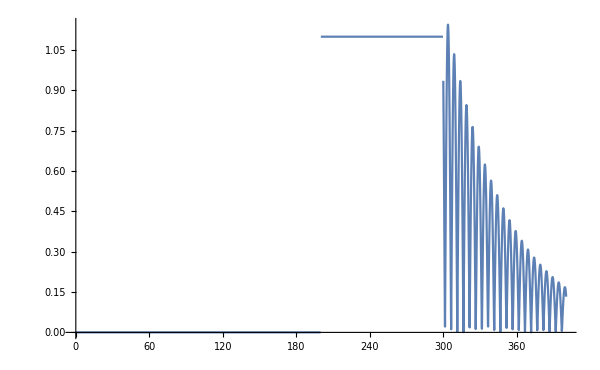

```mathematica
(* Empezemos definiendo la geometría y características de la linea de transmisión *)
y0=0;
y1=100;
l1=y1-y0;
y2=200;
l2=y2-y1;
y3=300;
l3=y3-y2;
y4=400.5;
l4=y4-y3;
lt=l1+l2+l3+l4;
r0=0.8 10^-3;
r1=5.2 10^-3;
r2=4 10^-3;
fg=0.5;
R[y_]:=If[y≤y1,r1,If[y≤y2,(r0-r1)/(y2-y1) y+(r1 y2-r0 y1)/(y2-y1),If[y≤ y3,r0,(Exp[fg lt] r0-r2 Exp[fg y3])/(Exp[fg lt]-Exp[fg y3])+(r2-r0)/(Exp[fg lt]-Exp[fg y3]) Exp[fg y]]]];
x0=0.7;
x1=1;
x2=5;
x3=11;
X[y_]:=If[y≤y1,(x1-x3)/y1 y+x3,If[y≤y2,x1,If[y≤ y3,(x1 √y3-x2 √y2+(x2-x1) √y)/(√y3-√y2),(x0 Exp[-y3]-x2 Exp[-lt]+(x2-x0) Exp[-y])/(Exp[-y3]-Exp[-lt])]]];
g0=7 10^-5;
g1=11 10^-5;
g2=0;
G[y_]:=If[y≤y1,g0,If[y≤y2,(g0 (y2^2-y^2))/(y2^2-y1^2),If[y≤ y3,g2,(g1 y+g2-g1 y3)/(lt-y3)]]];
b0=1;
θ=20 π;
bb=10/(y3-lt) Log[Abs[Sin[(θ y3)/(lt-y3)]]/Abs[Sin[(θ y3)/(lt-y3) lt]]];
B[y_]:=If[y≤y2,0,If[y≤ y3,1.1 b0,b0/(Exp[-bb y3]Abs[Sin[θ/(lt-y3)y3]])Exp[-bb y] Abs[Sin[θ/(lt-y3) y]]]];
{Plot[R[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[X[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[G[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[B[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600]}
```

```mathematica
R[x_]:=r
G[x_]:=g
```

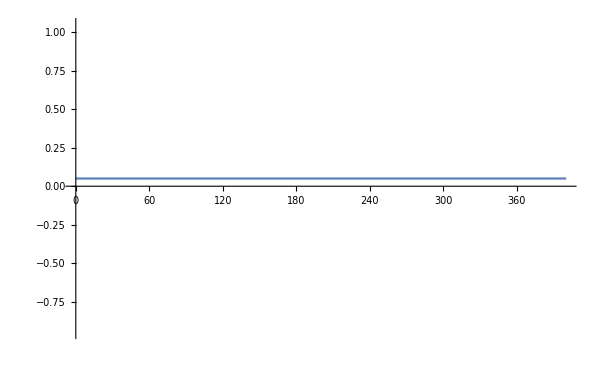
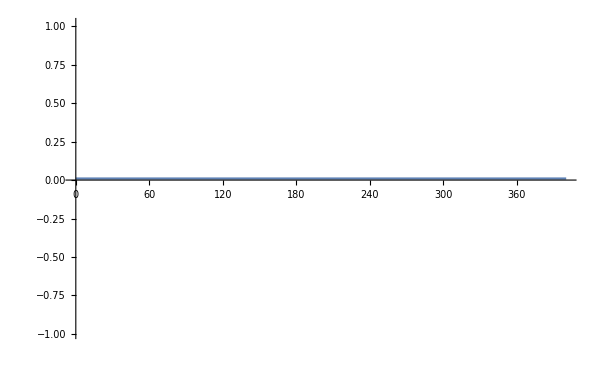
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Comprobemos a continuación que no hay problema en trabajar con la variable x como variable independiente *)
{Plot[R[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[X[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[G[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[B[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600]}
```

### Definición del funcional asociado

```mathematica
G[x]
```

0.01

```mathematica
Clear[x,F,FF]
(* denotaremos  y≡y1, y'≡p1, y''≡p2 y así sucesivamente *)
F[x_,y1_,p1_]:=1/R[x] p1^2+G[x] y1^2
FF[y_]:=∫_a^b F[x,y,D[y, x]]ⅆx
```

```mathematica
FF[y[x]]
```

∫_0^400.5 (0.01 y[x]^2+20. y'[x]^2)ⅆx

### Introducción de los extremos del intervalo y las condiciones de contorno de tipo Dirichlet de nuestro problema

```mathematica
a=y0;b=y4;
yb=VL; yL = yb
```

220

### Construcción de la partición del intervalo

Introducimos el número total de subintervalos, de igual longitud, en los que se subdivide el intervalo [a,b]. Pero en este caso concreto ya que sabemos que la solución debe ser una línea recta. Por tanto,  bastará con tomar el propio intervalo sin subdividir para obtener la solución exacta, como veremos más adelante.

```mathematica
n=100;
```

Y posteriormente se definen los nodos de la correspondiente partición uniforme del intervalo.

```mathematica
Clear[x,y,h]
h=(b-a)/n;
x[i_]:=a+i h
```

Y se implementan en los nodos extremos las condiciones de contorno de tipo Dirichlet introducidas previamente.

```mathematica
n
```

100

```mathematica
y[n]=yb;
```

### Cálculo de la función de varias variables que se va a optimizar y de sus puntos críticos

```mathematica
Clear[GG]
GG=Simplify[∑_(i=1)^n 
∫_x[i-1]^x[i] Expand[F[x,y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]]ⅆx]
```

242344.+5.00711 y[0]^2-9.97417 y[0] y[1]+10.0142 y[1]^2-9.97417 y[1] y[2]+10.0142 y[2]^2-9.97417 y[2] y[3]+10.0142 y[3]^2-9.97417 y[3] y[4]+10.0142 y[4]^2-9.97417 y[4] y[5]+10.0142 y[5]^2-9.97417 y[5] y[6]+10.0142 y[6]^2-9.97417 y[6] y[7]+10.0142 y[7]^2-9.97417 y[7] y[8]+10.0142 y[8]^2-9.97417 y[8] y[9]+10.0142 y[9]^2-9.97417 y[9] y[10]+10.0142 y[10]^2-9.97417 y[10] y[11]+10.0142 y[11]^2-9.97417 y[11] y[12]+10.0142 y[12]^2-9.97417 y[12] y[13]+10.0142 y[13]^2-9.97417 y[13] y[14]+10.0142 y[14]^2-9.97417 y[14] y[15]+10.0142 y[15]^2-9.97417 y[15] y[16]+10.0142 y[16]^2-9.97417 y[16] y[17]+10.0142 y[17]^2-9.97417 y[17] y[18]+10.0142 y[18]^2-9.97417 y[18] y[19]+10.0142 y[19]^2-9.97417 y[19] y[20]+10.0142 y[20]^2-9.97417 y[20] y[21]+10.0142 y[21]^2-9.97417 y[21] y[22]+10.0142 y[22]^2-9.97417 y[22] y[23]+10.0142 y[23]^2-9.97417 y[23] y[24]+10.0142 y[24]^2-9.97417 y[24] y[25]+10.0142 y[25]^2-9.97417 y[25] y[26]+10.0142 y[26]^2-9.97417 y[26] y[27]+10.0142 y[27]^2-9.97417 y[27] y[28]+10.0142 y[28]^2-9.97417 y[28] y[29]+10.0142 y[29]^2-9.97417 y[29] y[30]+10.0142 y[30]^2-9.97417 y[30] y[31]+10.0142 y[31]^2-9.97417 y[31] y[32]+10.0142 y[32]^2-9.97417 y[32] y[33]+10.0142 y[33]^2-9.97417 y[33] y[34]+10.0142 y[34]^2-9.97417 y[34] y[35]+10.0142 y[35]^2-9.97417 y[35] y[36]+10.0142 y[36]^2-9.97417 y[36] y[37]+10.0142 y[37]^2-9.97417 y[37] y[38]+10.0142 y[38]^2-9.97417 y[38] y[39]+10.0142 y[39]^2-9.97417 y[39] y[40]+10.0142 y[40]^2-9.97417 y[40] y[41]+10.0142 y[41]^2-9.97417 y[41] y[42]+10.0142 y[42]^2-9.97417 y[42] y[43]+10.0142 y[43]^2-9.97417 y[43] y[44]+10.0142 y[44]^2-9.97417 y[44] y[45]+10.0142 y[45]^2-9.97417 y[45] y[46]+10.0142 y[46]^2-9.97417 y[46] y[47]+10.0142 y[47]^2-9.97417 y[47] y[48]+10.0142 y[48]^2-9.97417 y[48] y[49]+10.0142 y[49]^2-9.97417 y[49] y[50]+10.0142 y[50]^2-9.97417 y[50] y[51]+10.0142 y[51]^2-9.97417 y[51] y[52]+10.0142 y[52]^2-9.97417 y[52] y[53]+10.0142 y[53]^2-9.97417 y[53] y[54]+10.0142 y[54]^2-9.97417 y[54] y[55]+10.0142 y[55]^2-9.97417 y[55] y[56]+10.0142 y[56]^2-9.97417 y[56] y[57]+10.0142 y[57]^2-9.97417 y[57] y[58]+10.0142 y[58]^2-9.97417 y[58] y[59]+10.0142 y[59]^2-9.97417 y[59] y[60]+10.0142 y[60]^2-9.97417 y[60] y[61]+10.0142 y[61]^2-9.97417 y[61] y[62]+10.0142 y[62]^2-9.97417 y[62] y[63]+10.0142 y[63]^2-9.97417 y[63] y[64]+10.0142 y[64]^2-9.97417 y[64] y[65]+10.0142 y[65]^2-9.97417 y[65] y[66]+10.0142 y[66]^2-9.97417 y[66] y[67]+10.0142 y[67]^2-9.97417 y[67] y[68]+10.0142 y[68]^2-9.97417 y[68] y[69]+10.0142 y[69]^2-9.97417 y[69] y[70]+10.0142 y[70]^2-9.97417 y[70] y[71]+10.0142 y[71]^2-9.97417 y[71] y[72]+10.0142 y[72]^2-9.97417 y[72] y[73]+10.0142 y[73]^2-9.97417 y[73] y[74]+10.0142 y[74]^2-9.97417 y[74] y[75]+10.0142 y[75]^2-9.97417 y[75] y[76]+10.0142 y[76]^2-9.97417 y[76] y[77]+10.0142 y[77]^2-9.97417 y[77] y[78]+10.0142 y[78]^2-9.97417 y[78] y[79]+10.0142 y[79]^2-9.97417 y[79] y[80]+10.0142 y[80]^2-9.97417 y[80] y[81]+10.0142 y[81]^2-9.97417 y[81] y[82]+10.0142 y[82]^2-9.97417 y[82] y[83]+10.0142 y[83]^2-9.97417 y[83] y[84]+10.0142 y[84]^2-9.97417 y[84] y[85]+10.0142 y[85]^2-9.97417 y[85] y[86]+10.0142 y[86]^2-9.97417 y[86] y[87]+10.0142 y[87]^2-9.97417 y[87] y[88]+10.0142 y[88]^2-9.97417 y[88] y[89]+10.0142 y[89]^2-9.97417 y[89] y[90]+10.0142 y[90]^2-9.97417 y[90] y[91]+10.0142 y[91]^2-9.97417 y[91] y[92]+10.0142 y[92]^2-9.97417 y[92] y[93]+10.0142 y[93]^2-9.97417 y[93] y[94]+10.0142 y[94]^2-9.97417 y[94] y[95]+10.0142 y[95]^2-9.97417 y[95] y[96]+10.0142 y[96]^2-9.97417 y[96] y[97]+10.0142 y[97]^2-9.97417 y[97] y[98]+10.0142 y[98]^2-2194.32 y[99]-9.97417 y[98] y[99]+10.0142 y[99]^2

```mathematica
ptoscrit1=Chop[NSolve[Table[D[GG, y[i]]==0,{i,0,n-1}],Table[y[i],{i,0,n-1}]]]
```

{{y[0]→0.0566042,y[1]→0.0568314,y[2]→0.0575151,y[3]→0.0586607,y[4]→0.0602774,y[5]→0.0623781,y[6]→0.0649798,y[7]→0.0681033,y[8]→0.0717737,y[9]→0.0760206,y[10]→0.0808779,y[11]→0.0863847,y[12]→0.0925853,y[13]→0.0995294,y[14]→0.107273,y[15]→0.115878,y[16]→0.125413,y[17]→0.135956,y[18]→0.14759,y[19]→0.16041,y[20]→0.174518,y[21]→0.190027,y[22]→0.207063,y[23]→0.225761,y[24]→0.246273,y[25]→0.268762,y[26]→0.293409,y[27]→0.320413,y[28]→0.34999,y[29]→0.382378,y[30]→0.417836,y[31]→0.45665,y[32]→0.499131,y[33]→0.545621,y[34]→0.596492,y[35]→0.652154,y[36]→0.713053,y[37]→0.779678,y[38]→0.852565,y[39]→0.932298,y[40]→1.01952,y[41]→1.11493,y[42]→1.21929,y[43]→1.33344,y[44]→1.4583,y[45]→1.59488,y[46]→1.74426,y[47]→1.90765,y[48]→2.08636,y[49]→2.28182,y[50]→2.49561,y[51]→2.72944,y[52]→2.98519,y[53]→3.26491,y[54]→3.57085,y[55]→3.90547,y[56]→4.27145,y[57]→4.67174,y[58]→5.10954,y[59]→5.58838,y[60]→6.1121,y[61]→6.6849,y[62]→7.31138,y[63]→7.99658,y[64]→8.746,y[65]→9.56566,y[66]→10.4621,y[67]→11.4426,y[68]→12.515,y[69]→13.6879,y[70]→14.9707,y[71]→16.3738,y[72]→17.9083,y[73]→19.5867,y[74]→21.4223,y[75]→23.43,y[76]→25.6258,y[77]→28.0275,y[78]→30.6542,y[79]→33.5271,y[80]→36.6693,y[81]→40.1059,y[82]→43.8646,y[83]→47.9756,y[84]→52.4718,y[85]→57.3895,y[86]→62.768,y[87]→68.6506,y[88]→75.0845,y[89]→82.1214,y[90]→89.8178,y[91]→98.2355,y[92]→107.442,y[93]→117.512,y[94]→128.525,y[95]→140.57,y[96]→153.744,y[97]→168.153,y[98]→183.912,y[99]→201.148}}

```mathematica
yy1=Table[y[i],{i,0,n}]/.ptoscrit1⟦1⟧
```

{0.0566042,0.0568314,0.0575151,0.0586607,0.0602774,0.0623781,0.0649798,0.0681033,0.0717737,0.0760206,0.0808779,0.0863847,0.0925853,0.0995294,0.107273,0.115878,0.125413,0.135956,0.14759,0.16041,0.174518,0.190027,0.207063,0.225761,0.246273,0.268762,0.293409,0.320413,0.34999,0.382378,0.417836,0.45665,0.499131,0.545621,0.596492,0.652154,0.713053,0.779678,0.852565,0.932298,1.01952,1.11493,1.21929,1.33344,1.4583,1.59488,1.74426,1.90765,2.08636,2.28182,2.49561,2.72944,2.98519,3.26491,3.57085,3.90547,4.27145,4.67174,5.10954,5.58838,6.1121,6.6849,7.31138,7.99658,8.746,9.56566,10.4621,11.4426,12.515,13.6879,14.9707,16.3738,17.9083,19.5867,21.4223,23.43,25.6258,28.0275,30.6542,33.5271,36.6693,40.1059,43.8646,47.9756,52.4718,57.3895,62.768,68.6506,75.0845,82.1214,89.8178,98.2355,107.442,117.512,128.525,140.57,153.744,168.153,183.912,201.148,220}

### Construcción de la poligonal correspondiente

```mathematica
yy1=Table[y[i],{i,0,n}]/.ptoscrit1⟦1⟧;
gg1=ListPlot[Table[{x[i],yy1⟦i+1⟧},{i,0,n}],PlotJoined->True,DisplayFunction->Identity]
```

-Graphics-

### Valor aproximado del extremo del funcional

```mathematica
valoraprox1energia =GG/.ptoscrit1⟦1⟧
```

21652.4

### Evaluación aproximada de la integral

Puede resultar muy conveniente usar una regla de cuadratura apropiada para evaluar mucho más fácilmente las integrales de la fórmula anterior. En este caso hemos implementado la conocida regla de los trapecios, obteniendo -como veremos- valores muy aceptables, con un esfuerzo computacional pequeño.

```mathematica
Clear[GGG]
GGG=∑_(i=1)^n 1/2 h (F[x[i-1],y[i-1],(y[i]-y[i-1])/h]+F[x[i],y[i],(y[i]-y[i-1])/h])
```

2.0025 (0.01 y[0]^2+0.01 y[1]^2+2.49376 (-y[0]+y[1])^2)+2.0025 (0.01 y[1]^2+0.01 y[2]^2+2.49376 (-y[1]+y[2])^2)+2.0025 (0.01 y[2]^2+0.01 y[3]^2+2.49376 (-y[2]+y[3])^2)+2.0025 (0.01 y[3]^2+0.01 y[4]^2+2.49376 (-y[3]+y[4])^2)+2.0025 (0.01 y[4]^2+0.01 y[5]^2+2.49376 (-y[4]+y[5])^2)+2.0025 (0.01 y[5]^2+0.01 y[6]^2+2.49376 (-y[5]+y[6])^2)+2.0025 (0.01 y[6]^2+0.01 y[7]^2+2.49376 (-y[6]+y[7])^2)+2.0025 (0.01 y[7]^2+0.01 y[8]^2+2.49376 (-y[7]+y[8])^2)+2.0025 (0.01 y[8]^2+0.01 y[9]^2+2.49376 (-y[8]+y[9])^2)+2.0025 (0.01 y[9]^2+0.01 y[10]^2+2.49376 (-y[9]+y[10])^2)+2.0025 (0.01 y[10]^2+0.01 y[11]^2+2.49376 (-y[10]+y[11])^2)+2.0025 (0.01 y[11]^2+0.01 y[12]^2+2.49376 (-y[11]+y[12])^2)+2.0025 (0.01 y[12]^2+0.01 y[13]^2+2.49376 (-y[12]+y[13])^2)+2.0025 (0.01 y[13]^2+0.01 y[14]^2+2.49376 (-y[13]+y[14])^2)+2.0025 (0.01 y[14]^2+0.01 y[15]^2+2.49376 (-y[14]+y[15])^2)+2.0025 (0.01 y[15]^2+0.01 y[16]^2+2.49376 (-y[15]+y[16])^2)+2.0025 (0.01 y[16]^2+0.01 y[17]^2+2.49376 (-y[16]+y[17])^2)+2.0025 (0.01 y[17]^2+0.01 y[18]^2+2.49376 (-y[17]+y[18])^2)+2.0025 (0.01 y[18]^2+0.01 y[19]^2+2.49376 (-y[18]+y[19])^2)+2.0025 (0.01 y[19]^2+0.01 y[20]^2+2.49376 (-y[19]+y[20])^2)+2.0025 (0.01 y[20]^2+0.01 y[21]^2+2.49376 (-y[20]+y[21])^2)+2.0025 (0.01 y[21]^2+0.01 y[22]^2+2.49376 (-y[21]+y[22])^2)+2.0025 (0.01 y[22]^2+0.01 y[23]^2+2.49376 (-y[22]+y[23])^2)+2.0025 (0.01 y[23]^2+0.01 y[24]^2+2.49376 (-y[23]+y[24])^2)+2.0025 (0.01 y[24]^2+0.01 y[25]^2+2.49376 (-y[24]+y[25])^2)+2.0025 (0.01 y[25]^2+0.01 y[26]^2+2.49376 (-y[25]+y[26])^2)+2.0025 (0.01 y[26]^2+0.01 y[27]^2+2.49376 (-y[26]+y[27])^2)+2.0025 (0.01 y[27]^2+0.01 y[28]^2+2.49376 (-y[27]+y[28])^2)+2.0025 (0.01 y[28]^2+0.01 y[29]^2+2.49376 (-y[28]+y[29])^2)+2.0025 (0.01 y[29]^2+0.01 y[30]^2+2.49376 (-y[29]+y[30])^2)+2.0025 (0.01 y[30]^2+0.01 y[31]^2+2.49376 (-y[30]+y[31])^2)+2.0025 (0.01 y[31]^2+0.01 y[32]^2+2.49376 (-y[31]+y[32])^2)+2.0025 (0.01 y[32]^2+0.01 y[33]^2+2.49376 (-y[32]+y[33])^2)+2.0025 (0.01 y[33]^2+0.01 y[34]^2+2.49376 (-y[33]+y[34])^2)+2.0025 (0.01 y[34]^2+0.01 y[35]^2+2.49376 (-y[34]+y[35])^2)+2.0025 (0.01 y[35]^2+0.01 y[36]^2+2.49376 (-y[35]+y[36])^2)+2.0025 (0.01 y[36]^2+0.01 y[37]^2+2.49376 (-y[36]+y[37])^2)+2.0025 (0.01 y[37]^2+0.01 y[38]^2+2.49376 (-y[37]+y[38])^2)+2.0025 (0.01 y[38]^2+0.01 y[39]^2+2.49376 (-y[38]+y[39])^2)+2.0025 (0.01 y[39]^2+0.01 y[40]^2+2.49376 (-y[39]+y[40])^2)+2.0025 (0.01 y[40]^2+0.01 y[41]^2+2.49376 (-y[40]+y[41])^2)+2.0025 (0.01 y[41]^2+0.01 y[42]^2+2.49376 (-y[41]+y[42])^2)+2.0025 (0.01 y[42]^2+0.01 y[43]^2+2.49376 (-y[42]+y[43])^2)+2.0025 (0.01 y[43]^2+0.01 y[44]^2+2.49376 (-y[43]+y[44])^2)+2.0025 (0.01 y[44]^2+0.01 y[45]^2+2.49376 (-y[44]+y[45])^2)+2.0025 (0.01 y[45]^2+0.01 y[46]^2+2.49376 (-y[45]+y[46])^2)+2.0025 (0.01 y[46]^2+0.01 y[47]^2+2.49376 (-y[46]+y[47])^2)+2.0025 (0.01 y[47]^2+0.01 y[48]^2+2.49376 (-y[47]+y[48])^2)+2.0025 (0.01 y[48]^2+0.01 y[49]^2+2.49376 (-y[48]+y[49])^2)+2.0025 (0.01 y[49]^2+0.01 y[50]^2+2.49376 (-y[49]+y[50])^2)+2.0025 (0.01 y[50]^2+0.01 y[51]^2+2.49376 (-y[50]+y[51])^2)+2.0025 (0.01 y[51]^2+0.01 y[52]^2+2.49376 (-y[51]+y[52])^2)+2.0025 (0.01 y[52]^2+0.01 y[53]^2+2.49376 (-y[52]+y[53])^2)+2.0025 (0.01 y[53]^2+0.01 y[54]^2+2.49376 (-y[53]+y[54])^2)+2.0025 (0.01 y[54]^2+0.01 y[55]^2+2.49376 (-y[54]+y[55])^2)+2.0025 (0.01 y[55]^2+0.01 y[56]^2+2.49376 (-y[55]+y[56])^2)+2.0025 (0.01 y[56]^2+0.01 y[57]^2+2.49376 (-y[56]+y[57])^2)+2.0025 (0.01 y[57]^2+0.01 y[58]^2+2.49376 (-y[57]+y[58])^2)+2.0025 (0.01 y[58]^2+0.01 y[59]^2+2.49376 (-y[58]+y[59])^2)+2.0025 (0.01 y[59]^2+0.01 y[60]^2+2.49376 (-y[59]+y[60])^2)+2.0025 (0.01 y[60]^2+0.01 y[61]^2+2.49376 (-y[60]+y[61])^2)+2.0025 (0.01 y[61]^2+0.01 y[62]^2+2.49376 (-y[61]+y[62])^2)+2.0025 (0.01 y[62]^2+0.01 y[63]^2+2.49376 (-y[62]+y[63])^2)+2.0025 (0.01 y[63]^2+0.01 y[64]^2+2.49376 (-y[63]+y[64])^2)+2.0025 (0.01 y[64]^2+0.01 y[65]^2+2.49376 (-y[64]+y[65])^2)+2.0025 (0.01 y[65]^2+0.01 y[66]^2+2.49376 (-y[65]+y[66])^2)+2.0025 (0.01 y[66]^2+0.01 y[67]^2+2.49376 (-y[66]+y[67])^2)+2.0025 (0.01 y[67]^2+0.01 y[68]^2+2.49376 (-y[67]+y[68])^2)+2.0025 (0.01 y[68]^2+0.01 y[69]^2+2.49376 (-y[68]+y[69])^2)+2.0025 (0.01 y[69]^2+0.01 y[70]^2+2.49376 (-y[69]+y[70])^2)+2.0025 (0.01 y[70]^2+0.01 y[71]^2+2.49376 (-y[70]+y[71])^2)+2.0025 (0.01 y[71]^2+0.01 y[72]^2+2.49376 (-y[71]+y[72])^2)+2.0025 (0.01 y[72]^2+0.01 y[73]^2+2.49376 (-y[72]+y[73])^2)+2.0025 (0.01 y[73]^2+0.01 y[74]^2+2.49376 (-y[73]+y[74])^2)+2.0025 (0.01 y[74]^2+0.01 y[75]^2+2.49376 (-y[74]+y[75])^2)+2.0025 (0.01 y[75]^2+0.01 y[76]^2+2.49376 (-y[75]+y[76])^2)+2.0025 (0.01 y[76]^2+0.01 y[77]^2+2.49376 (-y[76]+y[77])^2)+2.0025 (0.01 y[77]^2+0.01 y[78]^2+2.49376 (-y[77]+y[78])^2)+2.0025 (0.01 y[78]^2+0.01 y[79]^2+2.49376 (-y[78]+y[79])^2)+2.0025 (0.01 y[79]^2+0.01 y[80]^2+2.49376 (-y[79]+y[80])^2)+2.0025 (0.01 y[80]^2+0.01 y[81]^2+2.49376 (-y[80]+y[81])^2)+2.0025 (0.01 y[81]^2+0.01 y[82]^2+2.49376 (-y[81]+y[82])^2)+2.0025 (0.01 y[82]^2+0.01 y[83]^2+2.49376 (-y[82]+y[83])^2)+2.0025 (0.01 y[83]^2+0.01 y[84]^2+2.49376 (-y[83]+y[84])^2)+2.0025 (0.01 y[84]^2+0.01 y[85]^2+2.49376 (-y[84]+y[85])^2)+2.0025 (0.01 y[85]^2+0.01 y[86]^2+2.49376 (-y[85]+y[86])^2)+2.0025 (0.01 y[86]^2+0.01 y[87]^2+2.49376 (-y[86]+y[87])^2)+2.0025 (0.01 y[87]^2+0.01 y[88]^2+2.49376 (-y[87]+y[88])^2)+2.0025 (0.01 y[88]^2+0.01 y[89]^2+2.49376 (-y[88]+y[89])^2)+2.0025 (0.01 y[89]^2+0.01 y[90]^2+2.49376 (-y[89]+y[90])^2)+2.0025 (0.01 y[90]^2+0.01 y[91]^2+2.49376 (-y[90]+y[91])^2)+2.0025 (0.01 y[91]^2+0.01 y[92]^2+2.49376 (-y[91]+y[92])^2)+2.0025 (0.01 y[92]^2+0.01 y[93]^2+2.49376 (-y[92]+y[93])^2)+2.0025 (0.01 y[93]^2+0.01 y[94]^2+2.49376 (-y[93]+y[94])^2)+2.0025 (0.01 y[94]^2+0.01 y[95]^2+2.49376 (-y[94]+y[95])^2)+2.0025 (0.01 y[95]^2+0.01 y[96]^2+2.49376 (-y[95]+y[96])^2)+2.0025 (0.01 y[96]^2+0.01 y[97]^2+2.49376 (-y[96]+y[97])^2)+2.0025 (0.01 y[97]^2+0.01 y[98]^2+2.49376 (-y[97]+y[98])^2)+2.0025 (484.+2.49376 (220-y[99])^2+0.01 y[99]^2)+2.0025 (0.01 y[98]^2+0.01 y[99]^2+2.49376 (-y[98]+y[99])^2)

```mathematica
ptoscrit2=NSolve[Table[D[GGG, y[i]]==0,{i,0,n-1}],Table[y[i],{i,0,n-1}]]
```

{{y[0]→0.056944,y[1]→0.0571723,y[2]→0.0578592,y[3]→0.0590101,y[4]→0.0606342,y[5]→0.0627447,y[6]→0.0653583,y[7]→0.0684962,y[8]→0.0721834,y[9]→0.0764494,y[10]→0.0813287,y[11]→0.0868601,y[12]→0.0930882,y[13]→0.100063,y[14]→0.10784,y[15]→0.116482,y[16]→0.126058,y[17]→0.136646,y[18]→0.148329,y[19]→0.161201,y[20]→0.175367,y[21]→0.190939,y[22]→0.208042,y[23]→0.226814,y[24]→0.247405,y[25]→0.26998,y[26]→0.29472,y[27]→0.321824,y[28]→0.351509,y[29]→0.384013,y[30]→0.419597,y[31]→0.458546,y[32]→0.501173,y[33]→0.547819,y[34]→0.598859,y[35]→0.654701,y[36]→0.715794,y[37]→0.782628,y[38]→0.855739,y[39]→0.935712,y[40]→1.02319,y[41]→1.11887,y[42]→1.22353,y[43]→1.338,y[44]→1.4632,y[45]→1.60014,y[46]→1.74991,y[47]→1.91371,y[48]→2.09286,y[49]→2.2888,y[50]→2.50309,y[51]→2.73746,y[52]→2.99378,y[53]→3.27411,y[54]→3.5807,y[55]→3.91601,y[56]→4.28272,y[57]→4.68378,y[58]→5.12241,y[59]→5.60211,y[60]→6.12675,y[61]→6.70052,y[62]→7.32803,y[63]→8.01431,y[64]→8.76487,y[65]→9.58572,y[66]→10.4834,y[67]→11.4653,y[68]→12.539,y[69]→13.7133,y[70]→14.9976,y[71]→16.4022,y[72]→17.9383,y[73]→19.6183,y[74]→21.4557,y[75]→23.4651,y[76]→25.6627,y[77]→28.0661,y[78]→30.6946,y[79]→33.5693,y[80]→36.7132,y[81]→40.1515,y[82]→43.9119,y[83]→48.0244,y[84]→52.5221,y[85]→57.441,y[86]→62.8206,y[87]→68.704,y[88]→75.1384,y[89]→82.1755,y[90]→89.8715,y[91]→98.2884,y[92]→107.494,y[93]→117.561,y[94]→128.571,y[95]→140.612,y[96]→153.781,y[97]→168.183,y[98]→183.934,y[99]→201.16}}

```mathematica
yy2=Table[y[i],{i,0,n}]/.ptoscrit2⟦1⟧
gg2=ListPlot[Table[{x[i],yy2⟦i+1⟧},{i,0,n}],PlotJoined->True,DisplayFunction->Identity]
```

{0.056944,0.0571723,0.0578592,0.0590101,0.0606342,0.0627447,0.0653583,0.0684962,0.0721834,0.0764494,0.0813287,0.0868601,0.0930882,0.100063,0.10784,0.116482,0.126058,0.136646,0.148329,0.161201,0.175367,0.190939,0.208042,0.226814,0.247405,0.26998,0.29472,0.321824,0.351509,0.384013,0.419597,0.458546,0.501173,0.547819,0.598859,0.654701,0.715794,0.782628,0.855739,0.935712,1.02319,1.11887,1.22353,1.338,1.4632,1.60014,1.74991,1.91371,2.09286,2.2888,2.50309,2.73746,2.99378,3.27411,3.5807,3.91601,4.28272,4.68378,5.12241,5.60211,6.12675,6.70052,7.32803,8.01431,8.76487,9.58572,10.4834,11.4653,12.539,13.7133,14.9976,16.4022,17.9383,19.6183,21.4557,23.4651,25.6627,28.0661,30.6946,33.5693,36.7132,40.1515,43.9119,48.0244,52.5221,57.441,62.8206,68.704,75.1384,82.1755,89.8715,98.2884,107.494,117.561,128.571,140.612,153.781,168.183,183.934,201.16,220}

-Graphics-

```mathematica
valoraprox2energia =N[GGG/.ptoscrit2⟦1⟧]
```

21666.8

```mathematica
valoraprox1energia
```

21652.4

### Comparación de los valores obtenidos para las diferentes aproximaciones

```mathematica
TableForm[Table[{x[i],yy1⟦i+1⟧,yy2⟦i+1⟧},{i,0,n}],
TableHeadings->{None,
{"x[i] \n","y[i]  \n","y[i](trap.)\n"}}]
```

x[i] 
 | y[i]  
 | y[i](trap.)

0. | 0.0566042 | 0.056944
4.005 | 0.0568314 | 0.0571723
8.01 | 0.0575151 | 0.0578592
12.015 | 0.0586607 | 0.0590101
16.02 | 0.0602774 | 0.0606342
20.025 | 0.0623781 | 0.0627447
24.03 | 0.0649798 | 0.0653583
28.035 | 0.0681033 | 0.0684962
32.04 | 0.0717737 | 0.0721834
36.045 | 0.0760206 | 0.0764494
40.05 | 0.0808779 | 0.0813287
44.055 | 0.0863847 | 0.0868601
48.06 | 0.0925853 | 0.0930882
52.065 | 0.0995294 | 0.100063
56.07 | 0.107273 | 0.10784
60.075 | 0.115878 | 0.116482
64.08 | 0.125413 | 0.126058
68.085 | 0.135956 | 0.136646
72.09 | 0.14759 | 0.148329
76.095 | 0.16041 | 0.161201
80.1 | 0.174518 | 0.175367
84.105 | 0.190027 | 0.190939
88.11 | 0.207063 | 0.208042
92.115 | 0.225761 | 0.226814
96.12 | 0.246273 | 0.247405
100.125 | 0.268762 | 0.26998
104.13 | 0.293409 | 0.29472
108.135 | 0.320413 | 0.321824
112.14 | 0.34999 | 0.351509
116.145 | 0.382378 | 0.384013
120.15 | 0.417836 | 0.419597
124.155 | 0.45665 | 0.458546
128.16 | 0.499131 | 0.501173
132.165 | 0.545621 | 0.547819
136.17 | 0.596492 | 0.598859
140.175 | 0.652154 | 0.654701
144.18 | 0.713053 | 0.715794
148.185 | 0.779678 | 0.782628
152.19 | 0.852565 | 0.855739
156.195 | 0.932298 | 0.935712
160.2 | 1.01952 | 1.02319
164.205 | 1.11493 | 1.11887
168.21 | 1.21929 | 1.22353
172.215 | 1.33344 | 1.338
176.22 | 1.4583 | 1.4632
180.225 | 1.59488 | 1.60014
184.23 | 1.74426 | 1.74991
188.235 | 1.90765 | 1.91371
192.24 | 2.08636 | 2.09286
196.245 | 2.28182 | 2.2888
200.25 | 2.49561 | 2.50309
204.255 | 2.72944 | 2.73746
208.26 | 2.98519 | 2.99378
212.265 | 3.26491 | 3.27411
216.27 | 3.57085 | 3.5807
220.275 | 3.90547 | 3.91601
224.28 | 4.27145 | 4.28272
228.285 | 4.67174 | 4.68378
232.29 | 5.10954 | 5.12241
236.295 | 5.58838 | 5.60211
240.3 | 6.1121 | 6.12675
244.305 | 6.6849 | 6.70052
248.31 | 7.31138 | 7.32803
252.315 | 7.99658 | 8.01431
256.32 | 8.746 | 8.76487
260.325 | 9.56566 | 9.58572
264.33 | 10.4621 | 10.4834
268.335 | 11.4426 | 11.4653
272.34 | 12.515 | 12.539
276.345 | 13.6879 | 13.7133
280.35 | 14.9707 | 14.9976
284.355 | 16.3738 | 16.4022
288.36 | 17.9083 | 17.9383
292.365 | 19.5867 | 19.6183
296.37 | 21.4223 | 21.4557
300.375 | 23.43 | 23.4651
304.38 | 25.6258 | 25.6627
308.385 | 28.0275 | 28.0661
312.39 | 30.6542 | 30.6946
316.395 | 33.5271 | 33.5693
320.4 | 36.6693 | 36.7132
324.405 | 40.1059 | 40.1515
328.41 | 43.8646 | 43.9119
332.415 | 47.9756 | 48.0244
336.42 | 52.4718 | 52.5221
340.425 | 57.3895 | 57.441
344.43 | 62.768 | 62.8206
348.435 | 68.6506 | 68.704
352.44 | 75.0845 | 75.1384
356.445 | 82.1214 | 82.1755
360.45 | 89.8178 | 89.8715
364.455 | 98.2355 | 98.2884
368.46 | 107.442 | 107.494
372.465 | 117.512 | 117.561
376.47 | 128.525 | 128.571
380.475 | 140.57 | 140.612
384.48 | 153.744 | 153.781
388.485 | 168.153 | 168.183
392.49 | 183.912 | 183.934
396.495 | 201.148 | 201.16
400.5 | 220 | 220

### Comparación de los valores obtenidos para la solución exacta y las aproximaciones

```mathematica
TableForm[Table[{x[i],V[x[i]],yy1⟦i+1⟧,yy2⟦i+1⟧},{i,0,n}],
TableHeadings->{None,
{"x[i] \n","y[x[i]]  \n","y[i]  \n","y[i](trap.)\n"}}]
```

x[i] 
 | y[x[i]]  
 | y[i]  
 | y[i](trap.)

0. | 0.056774 | 0.0566042 | 0.056944
4.005 | 0.0570018 | 0.0568314 | 0.0571723
8.01 | 0.0576871 | 0.0575151 | 0.0578592
12.015 | 0.0588353 | 0.0586607 | 0.0590101
16.02 | 0.0604557 | 0.0602774 | 0.0606342
20.025 | 0.0625613 | 0.0623781 | 0.0627447
24.03 | 0.065169 | 0.0649798 | 0.0653583
28.035 | 0.0682996 | 0.0681033 | 0.0684962
32.04 | 0.0719784 | 0.0717737 | 0.0721834
36.045 | 0.0762349 | 0.0760206 | 0.0764494
40.05 | 0.0811032 | 0.0808779 | 0.0813287
44.055 | 0.0866223 | 0.0863847 | 0.0868601
48.06 | 0.0928367 | 0.0925853 | 0.0930882
52.065 | 0.099796 | 0.0995294 | 0.100063
56.07 | 0.107556 | 0.107273 | 0.10784
60.075 | 0.11618 | 0.115878 | 0.116482
64.08 | 0.125736 | 0.125413 | 0.126058
68.085 | 0.136301 | 0.135956 | 0.136646
72.09 | 0.147959 | 0.14759 | 0.148329
76.095 | 0.160806 | 0.16041 | 0.161201
80.1 | 0.174942 | 0.174518 | 0.175367
84.105 | 0.190483 | 0.190027 | 0.190939
88.11 | 0.207552 | 0.207063 | 0.208042
92.115 | 0.226288 | 0.225761 | 0.226814
96.12 | 0.246839 | 0.246273 | 0.247405
100.125 | 0.269371 | 0.268762 | 0.26998
104.13 | 0.294065 | 0.293409 | 0.29472
108.135 | 0.321119 | 0.320413 | 0.321824
112.14 | 0.35075 | 0.34999 | 0.351509
116.145 | 0.383195 | 0.382378 | 0.384013
120.15 | 0.418717 | 0.417836 | 0.419597
124.155 | 0.457598 | 0.45665 | 0.458546
128.16 | 0.500152 | 0.499131 | 0.501173
132.165 | 0.54672 | 0.545621 | 0.547819
136.17 | 0.597675 | 0.596492 | 0.598859
140.175 | 0.653427 | 0.652154 | 0.654701
144.18 | 0.714423 | 0.713053 | 0.715794
148.185 | 0.781153 | 0.779678 | 0.782628
152.19 | 0.854152 | 0.852565 | 0.855739
156.195 | 0.934005 | 0.932298 | 0.935712
160.2 | 1.02135 | 1.01952 | 1.02319
164.205 | 1.1169 | 1.11493 | 1.11887
168.21 | 1.22141 | 1.21929 | 1.22353
172.215 | 1.33572 | 1.33344 | 1.338
176.22 | 1.46075 | 1.4583 | 1.4632
180.225 | 1.59751 | 1.59488 | 1.60014
184.23 | 1.74708 | 1.74426 | 1.74991
188.235 | 1.91068 | 1.90765 | 1.91371
192.24 | 2.08961 | 2.08636 | 2.09286
196.245 | 2.28531 | 2.28182 | 2.2888
200.25 | 2.49935 | 2.49561 | 2.50309
204.255 | 2.73345 | 2.72944 | 2.73746
208.26 | 2.98948 | 2.98519 | 2.99378
212.265 | 3.26951 | 3.26491 | 3.27411
216.27 | 3.57578 | 3.57085 | 3.5807
220.275 | 3.91074 | 3.90547 | 3.91601
224.28 | 4.27709 | 4.27145 | 4.28272
228.285 | 4.67776 | 4.67174 | 4.68378
232.29 | 5.11598 | 5.10954 | 5.12241
236.295 | 5.59525 | 5.58838 | 5.60211
240.3 | 6.11943 | 6.1121 | 6.12675
244.305 | 6.69271 | 6.6849 | 6.70052
248.31 | 7.31971 | 7.31138 | 7.32803
252.315 | 8.00545 | 7.99658 | 8.01431
256.32 | 8.75544 | 8.746 | 8.76487
260.325 | 9.57569 | 9.56566 | 9.58572
264.33 | 10.4728 | 10.4621 | 10.4834
268.335 | 11.4539 | 11.4426 | 11.4653
272.34 | 12.527 | 12.515 | 12.539
276.345 | 13.7006 | 13.6879 | 13.7133
280.35 | 14.9842 | 14.9707 | 14.9976
284.355 | 16.388 | 16.3738 | 16.4022
288.36 | 17.9233 | 17.9083 | 17.9383
292.365 | 19.6025 | 19.5867 | 19.6183
296.37 | 21.439 | 21.4223 | 21.4557
300.375 | 23.4475 | 23.43 | 23.4651
304.38 | 25.6443 | 25.6258 | 25.6627
308.385 | 28.0468 | 28.0275 | 28.0661
312.39 | 30.6744 | 30.6542 | 30.6946
316.395 | 33.5482 | 33.5271 | 33.5693
320.4 | 36.6912 | 36.6693 | 36.7132
324.405 | 40.1287 | 40.1059 | 40.1515
328.41 | 43.8882 | 43.8646 | 43.9119
332.415 | 48. | 47.9756 | 48.0244
336.42 | 52.497 | 52.4718 | 52.5221
340.425 | 57.4152 | 57.3895 | 57.441
344.43 | 62.7943 | 62.768 | 62.8206
348.435 | 68.6773 | 68.6506 | 68.704
352.44 | 75.1115 | 75.0845 | 75.1384
356.445 | 82.1484 | 82.1214 | 82.1755
360.45 | 89.8447 | 89.8178 | 89.8715
364.455 | 98.262 | 98.2355 | 98.2884
368.46 | 107.468 | 107.442 | 107.494
372.465 | 117.536 | 117.512 | 117.561
376.47 | 128.548 | 128.525 | 128.571
380.475 | 140.591 | 140.57 | 140.612
384.48 | 153.763 | 153.744 | 153.781
388.485 | 168.168 | 168.153 | 168.183
392.49 | 183.923 | 183.912 | 183.934
396.495 | 201.154 | 201.148 | 201.16
400.5 | 220. | 220 | 220

#### Contraste gráfico

```mathematica
Show[gg1,gexact,DisplayFunction->$DisplayFunction]
```

-Graphics-

```mathematica
Show[gg2,gexact]
```

-Graphics-

```mathematica
Show[gg1,gg2]
```

-Graphics-

Comparamos en este gráfico las representaciones de la solución exacta, y la que proporcion el método de la poligonal de Euler, junto con la que se obtiene utilizando la regla de los trapecios para aproximar las integrales correspondientes.

#### Contraste gráfico

```mathematica
Show[gg1,gg2]
```

-Graphics-

Comparamos en este gráfico las representaciones de la solución que proporciona el método de la poligonal de Euler, junto con la que se obtiene utilizando la regla de los trapecios para aproximar las integrales correspondientes.

## Ejemplo con R y G variables

Resolveremos ahora otro problema de segundo orden, que proviene de la minimización del funcional energía correspondiente al caso en el que al menos R puede depender de la variable independiente, mientras que G, podría ser constante o no

		∂_x (1/(R(x))y'(x)) =  G(x) y(x), x∈[a,b]   (R(x) no supone que no se anula en todo caso)
		y’(a)=0 (cond. Neumann homogénea),  y(b)=y_b=V_L

 Habitualmente el intervalo en el que trabajaremos será [a,b]=[0,L].  Y podremos obtener también la solución de este problema de contorno como la única extremal del siguiente funcional energía asociado, que se puede ver que es estrictamente convexo y está definido como sigue

	L[y]=1/2∫_a^b (1/(R(x))y'(x)^2+G(x) (y(x))^2)dx       con y(b)=y_b (condición de tipo esencial que hay que imponer)
	
en un dominio de funciones, suficientemente regulares (ya sea de clase C^1, al menos a trozos y con derivada acotada, aunque no tenga porqué ser continua en todo el intervalo, como por ejemplo el espacio de los splines lineales de clase C^0, que además están incluidas en el correspondiente espacio más general en el que tiene sentido la definición del funcional, el denominado espacio de Sobolev H^1(a,b))

```mathematica
(* Empezemos definiendo la geometría y características de la linea de transmisión *)
y0=0;
y1=100;
l1=y1-y0;
y2=200;
l2=y2-y1;
y3=300;
l3=y3-y2;
y4=400.5;
l4=y4-y3;
lt=l1+l2+l3+l4;
r0=0.8 10^-3;
r1=5.2 10^-3;
r2=4 10^-3;
fg=0.5;
R[y_]:=If[y≤y1,r1,If[y≤y2,(r0-r1)/(y2-y1) y+(r1 y2-r0 y1)/(y2-y1),If[y≤ y3,r0,(Exp[fg lt] r0-r2 Exp[fg y3])/(Exp[fg lt]-Exp[fg y3])+(r2-r0)/(Exp[fg lt]-Exp[fg y3]) Exp[fg y]]]];
x0=0.7;
x1=1;
x2=5;
x3=11;
X[y_]:=If[y≤y1,(x1-x3)/y1 y+x3,If[y≤y2,x1,If[y≤ y3,(x1 √y3-x2 √y2+(x2-x1) √y)/(√y3-√y2),(x0 Exp[-y3]-x2 Exp[-lt]+(x2-x0) Exp[-y])/(Exp[-y3]-Exp[-lt])]]];
g0=7 10^-5;
g1=11 10^-5;
g2=0;
G[y_]:=If[y≤y1,g0,If[y≤y2,(g0 (y2^2-y^2))/(y2^2-y1^2),If[y≤ y3,g2,(g1 y+g2-g1 y3)/(lt-y3)]]];
b0=1;
θ=20 π;
bb=10/(y3-lt) Log[Abs[Sin[(θ y3)/(lt-y3)]]/Abs[Sin[(θ y3)/(lt-y3) lt]]];
B[y_]:=If[y≤y2,0,If[y≤ y3,1.1 b0,b0/(Exp[-bb y3]Abs[Sin[θ/(lt-y3)y3]])Exp[-bb y] Abs[Sin[θ/(lt-y3) y]]]];
{Plot[R[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[X[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[G[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[B[y],{y,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Comprobemos a continuación que no hay problema en trabajar con la variable x como variable independiente *)
{Plot[R[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[X[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[G[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600],
Plot[B[x],{x,y0,y4},PlotRange->All, LabelStyle->Directive[Bold, FontSize -> 26],ImageSize->600]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Definición del funcional asociado

```mathematica
G[x]
```

If[x≤100,g0,If[x≤y2,(g0 (y2^2-x^2))/(y2^2-y1^2),If[x≤y3,g2,(g1 x+g2-g1 y3)/(lt-y3)]]]

```mathematica
Clear[x,F,FF]
(* denotaremos  y≡y1, y'≡p1, y''≡p2 y así sucesivamente *)
F[x_,y1_,p1_]:=1/R[x] p1^2+G[x] y1^2
FF[y_]:=∫_a^b F[x,y,D[y, x]]ⅆx
```

```mathematica
FF[y[x]]
```

∫_0^400.5 (If[x≤100,g0,If[x≤y2,(g0 (y2^2-x^2))/(y2^2-y1^2),If[x≤y3,g2,(g1 x+g2-g1 y3)/(lt-y3)]]] y[x]^2+y'[x]^2/If[x≤100,r1,If[x≤y2,((r0-r1) x)/(y2-y1)+(r1 y2-r0 y1)/(y2-y1),If[x≤y3,r0,(Exp[fg lt] r0-r2 Exp[fg y3])/(Exp[fg lt]-Exp[fg y3])+((r2-r0) Exp[fg x])/(Exp[fg lt]-Exp[fg y3])]]])ⅆx

### Introducción de los extremos del intervalo y las condiciones de contorno de tipo Dirichlet de nuestro problema

```mathematica
a=y0;b=y4;
yb=VL; yL = yb
```

220

### Construcción de la partición del intervalo

Introducimos el número total de subintervalos, de igual longitud, en los que se subdivide el intervalo [a,b]. Pero en este caso concreto ya que sabemos que la solución debe ser una línea recta. Por tanto,  bastará con tomar el propio intervalo sin subdividir para obtener la solución exacta, como veremos más adelante.

```mathematica
n=100;
```

Y posteriormente se definen los nodos de la correspondiente partición uniforme del intervalo.

```mathematica
Clear[x,y,h]
h=(b-a)/n;
x[i_]:=a+i h
```

Y se implementan en los nodos extremos las condiciones de contorno de tipo Dirichlet introducidas previamente.

```mathematica
n
```

100

```mathematica
y[n]=yb;
```

### Cálculo de la función de varias variables que se va a optimizar y de sus puntos críticos

```mathematica
Clear[GG]
GG=Simplify[∑_(i=1)^n 
∫_x[i-1]^x[i] Expand[F[x,y[i-1]+((x-x[i-1]) (y[i]-y[i-1]))/h,(y[i]-y[i-1])/h]]ⅆx]
```

6.22228×10^6+48.017 y[0]^2-96.0337 y[0] y[1]+96.034 y[1]^2-96.0337 y[1] y[2]+96.034 y[2]^2-96.0337 y[2] y[3]+96.034 y[3]^2-96.0337 y[3] y[4]+96.034 y[4]^2-96.0337 y[4] y[5]+96.034 y[5]^2-96.0337 y[5] y[6]+96.034 y[6]^2-96.0337 y[6] y[7]+96.034 y[7]^2-96.0337 y[7] y[8]+96.034 y[8]^2-96.0337 y[8] y[9]+96.034 y[9]^2-96.0337 y[9] y[10]+96.034 y[10]^2-96.0337 y[10] y[11]+96.034 y[11]^2-96.0337 y[11] y[12]+96.034 y[12]^2-96.0337 y[12] y[13]+96.034 y[13]^2-96.0337 y[13] y[14]+96.034 y[14]^2-96.0337 y[14] y[15]+96.034 y[15]^2-96.0337 y[15] y[16]+96.034 y[16]^2-96.0337 y[16] y[17]+96.034 y[17]^2-96.0337 y[17] y[18]+96.034 y[18]^2-96.0337 y[18] y[19]+96.034 y[19]^2-96.0337 y[19] y[20]+96.034 y[20]^2-96.0337 y[20] y[21]+96.034 y[21]^2-96.0337 y[21] y[22]+96.034 y[22]^2-96.0337 y[22] y[23]+96.034 y[23]^2-96.0337 y[23] y[24]+96.0348 y[24]^2-96.0353 y[24] y[25]+96.9199 y[25]^2-97.8039 y[25] y[26]+99.5525 y[26]^2-101.3 y[26] y[27]+103.179 y[27]^2-105.056 y[27] y[28]+107.079 y[28]^2-109.101 y[28] y[29]+111.286 y[29]^2-113.471 y[29] y[30]+115.838 y[30]^2-118.204 y[30] y[31]+120.778 y[31]^2-123.35 y[31] y[32]+126.158 y[32]^2-128.965 y[32] y[33]+132.04 y[33]^2-135.115 y[33] y[34]+138.498 y[34]^2-141.881 y[34] y[35]+145.621 y[35]^2-149.361 y[35] y[36]+153.517 y[36]^2-157.673 y[36] y[37]+162.32 y[37]^2-166.966 y[37] y[38]+172.194 y[38]^2-177.423 y[38] y[39]+183.35 y[39]^2-189.277 y[39] y[40]+196.054 y[40]^2-202.83 y[40] y[41]+210.652 y[41]^2-218.475 y[41] y[42]+227.605 y[42]^2-236.736 y[42] y[43]+247.533 y[43]^2-258.33 y[43] y[44]+271.297 y[44]^2-284.263 y[44] y[45]+300.127 y[45]^2-315.99 y[45] y[46]+335.845 y[46]^2-355.699 y[46] y[47]+381.271 y[47]^2-406.843 y[47] y[48]+441.023 y[48]^2-475.203 y[48] y[49]+523.101 y[49]^2-570.999 y[49] y[50]+597.609 y[50]^2-624.22 y[50] y[51]+624.22 y[51]^2-624.22 y[51] y[52]+624.22 y[52]^2-624.22 y[52] y[53]+624.22 y[53]^2-624.22 y[53] y[54]+624.22 y[54]^2-624.22 y[54] y[55]+624.22 y[55]^2-624.22 y[55] y[56]+624.22 y[56]^2-624.22 y[56] y[57]+624.22 y[57]^2-624.22 y[57] y[58]+624.22 y[58]^2-624.22 y[58] y[59]+624.22 y[59]^2-624.22 y[59] y[60]+624.22 y[60]^2-624.22 y[60] y[61]+624.22 y[61]^2-624.22 y[61] y[62]+624.22 y[62]^2-624.22 y[62] y[63]+624.22 y[63]^2-624.22 y[63] y[64]+624.22 y[64]^2-624.22 y[64] y[65]+624.22 y[65]^2-624.22 y[65] y[66]+624.22 y[66]^2-624.22 y[66] y[67]+624.22 y[67]^2-624.22 y[67] y[68]+624.22 y[68]^2-624.22 y[68] y[69]+624.22 y[69]^2-624.22 y[69] y[70]+624.22 y[70]^2-624.22 y[70] y[71]+624.22 y[71]^2-624.22 y[71] y[72]+624.22 y[72]^2-624.22 y[72] y[73]+624.22 y[73]^2-624.22 y[73] y[74]+624.22 y[74]^2-624.22 y[74] y[75]+624.22 y[75]^2-624.22 y[75] y[76]+624.22 y[76]^2-624.22 y[76] y[77]+624.22 y[77]^2-624.22 y[77] y[78]+624.22 y[78]^2-624.22 y[78] y[79]+624.22 y[79]^2-624.22 y[79] y[80]+624.22 y[80]^2-624.22 y[80] y[81]+624.22 y[81]^2-624.22 y[81] y[82]+624.22 y[82]^2-624.22 y[82] y[83]+624.22 y[83]^2-624.22 y[83] y[84]+624.22 y[84]^2-624.22 y[84] y[85]+624.22 y[85]^2-624.22 y[85] y[86]+624.22 y[86]^2-624.22 y[86] y[87]+624.22 y[87]^2-624.22 y[87] y[88]+624.22 y[88]^2-624.22 y[88] y[89]+624.22 y[89]^2-624.22 y[89] y[90]+624.22 y[90]^2-624.22 y[90] y[91]+624.22 y[91]^2-624.22 y[91] y[92]+624.219 y[92]^2-624.219 y[92] y[93]+624.216 y[93]^2-624.213 y[93] y[94]+624.193 y[94]^2-624.171 y[94] y[95]+624.017 y[95]^2-623.862 y[95] y[96]+622.722 y[96]^2-621.581 y[96] y[97]+613.46 y[97]^2-605.339 y[97] y[98]+558.45 y[98]^2-56566.1 y[99]-511.56 y[98] y[99]+384.34 y[99]^2

```mathematica
ptoscrit1=Chop[NSolve[Table[D[GG, y[i]]==0,{i,0,n-1}],Table[y[i],{i,0,n-1}]]]
```

{{y[0]→218.575,y[1]→218.575,y[2]→218.577,y[3]→218.58,y[4]→218.585,y[5]→218.591,y[6]→218.598,y[7]→218.606,y[8]→218.616,y[9]→218.626,y[10]→218.639,y[11]→218.652,y[12]→218.667,y[13]→218.683,y[14]→218.7,y[15]→218.718,y[16]→218.738,y[17]→218.759,y[18]→218.781,y[19]→218.805,y[20]→218.83,y[21]→218.856,y[22]→218.884,y[23]→218.912,y[24]→218.942,y[25]→218.974,y[26]→219.006,y[27]→219.038,y[28]→219.07,y[29]→219.101,y[30]→219.133,y[31]→219.164,y[32]→219.195,y[33]→219.225,y[34]→219.255,y[35]→219.283,y[36]→219.311,y[37]→219.338,y[38]→219.363,y[39]→219.388,y[40]→219.412,y[41]→219.434,y[42]→219.455,y[43]→219.474,y[44]→219.492,y[45]→219.508,y[46]→219.523,y[47]→219.536,y[48]→219.548,y[49]→219.558,y[50]→219.567,y[51]→219.574,y[52]→219.582,y[53]→219.589,y[54]→219.597,y[55]→219.605,y[56]→219.612,y[57]→219.62,y[58]→219.628,y[59]→219.635,y[60]→219.643,y[61]→219.651,y[62]→219.658,y[63]→219.666,y[64]→219.673,y[65]→219.681,y[66]→219.689,y[67]→219.696,y[68]→219.704,y[69]→219.712,y[70]→219.719,y[71]→219.727,y[72]→219.735,y[73]→219.742,y[74]→219.75,y[75]→219.757,y[76]→219.765,y[77]→219.773,y[78]→219.78,y[79]→219.788,y[80]→219.796,y[81]→219.804,y[82]→219.812,y[83]→219.82,y[84]→219.828,y[85]→219.836,y[86]→219.844,y[87]→219.853,y[88]→219.861,y[89]→219.87,y[90]→219.879,y[91]→219.888,y[92]→219.898,y[93]→219.907,y[94]→219.917,y[95]→219.927,y[96]→219.937,y[97]→219.948,y[98]→219.959,y[99]→219.972}}

```mathematica
yy1=Table[y[i],{i,0,n}]/.ptoscrit1⟦1⟧
```

{218.575,218.575,218.577,218.58,218.585,218.591,218.598,218.606,218.616,218.626,218.639,218.652,218.667,218.683,218.7,218.718,218.738,218.759,218.781,218.805,218.83,218.856,218.884,218.912,218.942,218.974,219.006,219.038,219.07,219.101,219.133,219.164,219.195,219.225,219.255,219.283,219.311,219.338,219.363,219.388,219.412,219.434,219.455,219.474,219.492,219.508,219.523,219.536,219.548,219.558,219.567,219.574,219.582,219.589,219.597,219.605,219.612,219.62,219.628,219.635,219.643,219.651,219.658,219.666,219.673,219.681,219.689,219.696,219.704,219.712,219.719,219.727,219.735,219.742,219.75,219.757,219.765,219.773,219.78,219.788,219.796,219.804,219.812,219.82,219.828,219.836,219.844,219.853,219.861,219.87,219.879,219.888,219.898,219.907,219.917,219.927,219.937,219.948,219.959,219.972,220}

### Construcción de la poligonal correspondiente

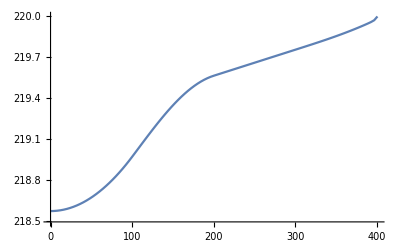

```mathematica
yy1=Table[y[i],{i,0,n}]/.ptoscrit1⟦1⟧;
gg1=ListPlot[Table[{x[i],yy1⟦i+1⟧},{i,0,n}],PlotJoined->True,DisplayFunction->Identity]
```

### Valor aproximado del extremo del funcional

```mathematica
valoraprox1energia =GG/.ptoscrit1⟦1⟧
```

791.782

### Evaluación aproximada de la integral

Puede resultar muy conveniente usar una regla de cuadratura apropiada para evaluar mucho más fácilmente las integrales de la fórmula anterior. En este caso hemos implementado la conocida regla de los trapecios, obteniendo -como veremos- valores muy aceptables, con un esfuerzo computacional pequeño.

```mathematica
Clear[GGG]
GGG=∑_(i=1)^n 1/2 h (F[x[i-1],y[i-1],(y[i]-y[i-1])/h]+F[x[i],y[i],(y[i]-y[i-1])/h])
```

2.0025 ((7 y[0]^2)/100000+(7 y[1]^2)/100000+23.9785 (-y[0]+y[1])^2)+2.0025 ((7 y[1]^2)/100000+(7 y[2]^2)/100000+23.9785 (-y[1]+y[2])^2)+2.0025 ((7 y[2]^2)/100000+(7 y[3]^2)/100000+23.9785 (-y[2]+y[3])^2)+2.0025 ((7 y[3]^2)/100000+(7 y[4]^2)/100000+23.9785 (-y[3]+y[4])^2)+2.0025 ((7 y[4]^2)/100000+(7 y[5]^2)/100000+23.9785 (-y[4]+y[5])^2)+2.0025 ((7 y[5]^2)/100000+(7 y[6]^2)/100000+23.9785 (-y[5]+y[6])^2)+2.0025 ((7 y[6]^2)/100000+(7 y[7]^2)/100000+23.9785 (-y[6]+y[7])^2)+2.0025 ((7 y[7]^2)/100000+(7 y[8]^2)/100000+23.9785 (-y[7]+y[8])^2)+2.0025 ((7 y[8]^2)/100000+(7 y[9]^2)/100000+23.9785 (-y[8]+y[9])^2)+2.0025 ((7 y[9]^2)/100000+(7 y[10]^2)/100000+23.9785 (-y[9]+y[10])^2)+2.0025 ((7 y[10]^2)/100000+(7 y[11]^2)/100000+23.9785 (-y[10]+y[11])^2)+2.0025 ((7 y[11]^2)/100000+(7 y[12]^2)/100000+23.9785 (-y[11]+y[12])^2)+2.0025 ((7 y[12]^2)/100000+(7 y[13]^2)/100000+23.9785 (-y[12]+y[13])^2)+2.0025 ((7 y[13]^2)/100000+(7 y[14]^2)/100000+23.9785 (-y[13]+y[14])^2)+2.0025 ((7 y[14]^2)/100000+(7 y[15]^2)/100000+23.9785 (-y[14]+y[15])^2)+2.0025 ((7 y[15]^2)/100000+(7 y[16]^2)/100000+23.9785 (-y[15]+y[16])^2)+2.0025 ((7 y[16]^2)/100000+(7 y[17]^2)/100000+23.9785 (-y[16]+y[17])^2)+2.0025 ((7 y[17]^2)/100000+(7 y[18]^2)/100000+23.9785 (-y[17]+y[18])^2)+2.0025 ((7 y[18]^2)/100000+(7 y[19]^2)/100000+23.9785 (-y[18]+y[19])^2)+2.0025 ((7 y[19]^2)/100000+(7 y[20]^2)/100000+23.9785 (-y[19]+y[20])^2)+2.0025 ((7 y[20]^2)/100000+(7 y[21]^2)/100000+23.9785 (-y[20]+y[21])^2)+2.0025 ((7 y[21]^2)/100000+(7 y[22]^2)/100000+23.9785 (-y[21]+y[22])^2)+2.0025 ((7 y[22]^2)/100000+(7 y[23]^2)/100000+23.9785 (-y[22]+y[23])^2)+2.0025 ((7 y[23]^2)/100000+(7 y[24]^2)/100000+23.9785 (-y[23]+y[24])^2)+2.0025 ((7 y[24]^2)/100000+0.0000699416 y[25]^2+23.9912 (-y[24]+y[25])^2)+2.0025 (0.0000699416 y[25]^2+0.0000680329 y[26]^2+24.4253 (-y[25]+y[26])^2)+2.0025 (0.0000680329 y[26]^2+0.0000660493 y[27]^2+25.2989 (-y[26]+y[27])^2)+2.0025 (0.0000660493 y[27]^2+0.0000639908 y[28]^2+26.2373 (-y[27]+y[28])^2)+2.0025 (0.0000639908 y[28]^2+0.0000618575 y[29]^2+27.2481 (-y[28]+y[29])^2)+2.0025 (0.0000618575 y[29]^2+0.0000596493 y[30]^2+28.3398 (-y[29]+y[30])^2)+2.0025 (0.0000596493 y[30]^2+0.0000573663 y[31]^2+29.5228 (-y[30]+y[31])^2)+2.0025 (0.0000573663 y[31]^2+0.0000550084 y[32]^2+30.8088 (-y[31]+y[32])^2)+2.0025 (0.0000550084 y[32]^2+0.0000525756 y[33]^2+32.2121 (-y[32]+y[33])^2)+2.0025 (0.0000525756 y[33]^2+0.000050068 y[34]^2+33.7494 (-y[33]+y[34])^2)+2.0025 (0.000050068 y[34]^2+0.0000474856 y[35]^2+35.4408 (-y[34]+y[35])^2)+2.0025 (0.0000474856 y[35]^2+0.0000448283 y[36]^2+37.3109 (-y[35]+y[36])^2)+2.0025 (0.0000448283 y[36]^2+0.0000420961 y[37]^2+39.3895 (-y[36]+y[37])^2)+2.0025 (0.0000420961 y[37]^2+0.0000392891 y[38]^2+41.7135 (-y[37]+y[38])^2)+2.0025 (0.0000392891 y[38]^2+0.0000364073 y[39]^2+44.3292 (-y[38]+y[39])^2)+2.0025 (0.0000364073 y[39]^2+0.0000334506 y[40]^2+47.2954 (-y[39]+y[40])^2)+2.0025 (0.0000334506 y[40]^2+0.000030419 y[41]^2+50.6875 (-y[40]+y[41])^2)+2.0025 (0.000030419 y[41]^2+0.0000273126 y[42]^2+54.6045 (-y[41]+y[42])^2)+2.0025 (0.0000273126 y[42]^2+0.0000241313 y[43]^2+59.1788 (-y[42]+y[43])^2)+2.0025 (0.0000241313 y[43]^2+0.0000208752 y[44]^2+64.5913 (-y[43]+y[44])^2)+2.0025 (0.0000208752 y[44]^2+0.0000175442 y[45]^2+71.0962 (-y[44]+y[45])^2)+2.0025 (0.0000175442 y[45]^2+0.0000141384 y[46]^2+79.0625 (-y[45]+y[46])^2)+2.0025 (0.0000141384 y[46]^2+0.0000106577 y[47]^2+89.0472 (-y[46]+y[47])^2)+2.0025 (0.0000106577 y[47]^2+7.10216×10^-6 y[48]^2+101.933 (-y[47]+y[48])^2)+2.0025 (7.10216×10^-6 y[48]^2+3.47177×10^-6 y[49]^2+119.209 (-y[48]+y[49])^2)+2.0025 (3.47177×10^-6 y[49]^2+142.521 (-y[49]+y[50])^2)+312.11 (-y[50]+y[51])^2+312.11 (-y[51]+y[52])^2+312.11 (-y[52]+y[53])^2+312.11 (-y[53]+y[54])^2+312.11 (-y[54]+y[55])^2+312.11 (-y[55]+y[56])^2+312.11 (-y[56]+y[57])^2+312.11 (-y[57]+y[58])^2+312.11 (-y[58]+y[59])^2+312.11 (-y[59]+y[60])^2+312.11 (-y[60]+y[61])^2+312.11 (-y[61]+y[62])^2+312.11 (-y[62]+y[63])^2+312.11 (-y[63]+y[64])^2+312.11 (-y[64]+y[65])^2+312.11 (-y[65]+y[66])^2+312.11 (-y[66]+y[67])^2+312.11 (-y[67]+y[68])^2+312.11 (-y[68]+y[69])^2+312.11 (-y[69]+y[70])^2+312.11 (-y[70]+y[71])^2+312.11 (-y[71]+y[72])^2+312.11 (-y[72]+y[73])^2+312.11 (-y[73]+y[74])^2+2.0025 (4.10448×10^-7 y[75]^2+155.86 (-y[74]+y[75])^2)+2.0025 (4.10448×10^-7 y[75]^2+4.79403×10^-6 y[76]^2+155.86 (-y[75]+y[76])^2)+2.0025 (4.79403×10^-6 y[76]^2+9.17761×10^-6 y[77]^2+155.86 (-y[76]+y[77])^2)+2.0025 (9.17761×10^-6 y[77]^2+0.0000135612 y[78]^2+155.86 (-y[77]+y[78])^2)+2.0025 (0.0000135612 y[78]^2+0.0000179448 y[79]^2+155.86 (-y[78]+y[79])^2)+2.0025 (0.0000179448 y[79]^2+0.0000223284 y[80]^2+155.86 (-y[79]+y[80])^2)+2.0025 (0.0000223284 y[80]^2+0.0000267119 y[81]^2+155.86 (-y[80]+y[81])^2)+2.0025 (0.0000267119 y[81]^2+0.0000310955 y[82]^2+155.86 (-y[81]+y[82])^2)+2.0025 (0.0000310955 y[82]^2+0.0000354791 y[83]^2+155.86 (-y[82]+y[83])^2)+2.0025 (0.0000354791 y[83]^2+0.0000398627 y[84]^2+155.86 (-y[83]+y[84])^2)+2.0025 (0.0000398627 y[84]^2+0.0000442463 y[85]^2+155.86 (-y[84]+y[85])^2)+2.0025 (0.0000442463 y[85]^2+0.0000486299 y[86]^2+155.86 (-y[85]+y[86])^2)+2.0025 (0.0000486299 y[86]^2+0.0000530134 y[87]^2+155.86 (-y[86]+y[87])^2)+2.0025 (0.0000530134 y[87]^2+0.000057397 y[88]^2+155.86 (-y[87]+y[88])^2)+2.0025 (0.000057397 y[88]^2+0.0000617806 y[89]^2+155.86 (-y[88]+y[89])^2)+2.0025 (0.0000617806 y[89]^2+0.0000661642 y[90]^2+155.86 (-y[89]+y[90])^2)+2.0025 (0.0000661642 y[90]^2+0.0000705478 y[91]^2+155.86 (-y[90]+y[91])^2)+2.0025 (0.0000705478 y[91]^2+0.0000749313 y[92]^2+155.86 (-y[91]+y[92])^2)+2.0025 (0.0000749313 y[92]^2+0.0000793149 y[93]^2+155.86 (-y[92]+y[93])^2)+2.0025 (0.0000793149 y[93]^2+0.0000836985 y[94]^2+155.858 (-y[93]+y[94])^2)+2.0025 (0.0000836985 y[94]^2+0.0000880821 y[95]^2+155.844 (-y[94]+y[95])^2)+2.0025 (0.0000880821 y[95]^2+0.0000924657 y[96]^2+155.743 (-y[95]+y[96])^2)+2.0025 (0.0000924657 y[96]^2+0.0000968493 y[97]^2+154.997 (-y[96]+y[97])^2)+2.0025 (0.0000968493 y[97]^2+0.000101233 y[98]^2+149.806 (-y[97]+y[98])^2)+2.0025 (5.324+66.1903 (220-y[99])^2+0.000105616 y[99]^2)+2.0025 (0.000101233 y[98]^2+0.000105616 y[99]^2+123.239 (-y[98]+y[99])^2)

```mathematica
ptoscrit2=NSolve[Table[D[GGG, y[i]]==0,{i,0,n-1}],Table[y[i],{i,0,n-1}]]
```

{{y[0]→218.575,y[1]→218.576,y[2]→218.578,y[3]→218.581,y[4]→218.586,y[5]→218.591,y[6]→218.598,y[7]→218.607,y[8]→218.616,y[9]→218.627,y[10]→218.639,y[11]→218.653,y[12]→218.667,y[13]→218.683,y[14]→218.7,y[15]→218.719,y[16]→218.739,y[17]→218.76,y[18]→218.782,y[19]→218.806,y[20]→218.831,y[21]→218.857,y[22]→218.884,y[23]→218.913,y[24]→218.943,y[25]→218.974,y[26]→219.006,y[27]→219.038,y[28]→219.07,y[29]→219.102,y[30]→219.134,y[31]→219.165,y[32]→219.196,y[33]→219.226,y[34]→219.255,y[35]→219.284,y[36]→219.311,y[37]→219.338,y[38]→219.364,y[39]→219.389,y[40]→219.412,y[41]→219.434,y[42]→219.455,y[43]→219.474,y[44]→219.492,y[45]→219.509,y[46]→219.524,y[47]→219.537,y[48]→219.548,y[49]→219.558,y[50]→219.567,y[51]→219.574,y[52]→219.582,y[53]→219.59,y[54]→219.597,y[55]→219.605,y[56]→219.613,y[57]→219.62,y[58]→219.628,y[59]→219.636,y[60]→219.643,y[61]→219.651,y[62]→219.658,y[63]→219.666,y[64]→219.674,y[65]→219.681,y[66]→219.689,y[67]→219.697,y[68]→219.704,y[69]→219.712,y[70]→219.72,y[71]→219.727,y[72]→219.735,y[73]→219.742,y[74]→219.75,y[75]→219.758,y[76]→219.765,y[77]→219.773,y[78]→219.781,y[79]→219.788,y[80]→219.796,y[81]→219.804,y[82]→219.812,y[83]→219.82,y[84]→219.828,y[85]→219.836,y[86]→219.845,y[87]→219.853,y[88]→219.862,y[89]→219.87,y[90]→219.879,y[91]→219.888,y[92]→219.898,y[93]→219.907,y[94]→219.917,y[95]→219.927,y[96]→219.937,y[97]→219.948,y[98]→219.959,y[99]→219.973}}

{218.575,218.576,218.578,218.581,218.586,218.591,218.598,218.607,218.616,218.627,218.639,218.653,218.667,218.683,218.7,218.719,218.739,218.76,218.782,218.806,218.831,218.857,218.884,218.913,218.943,218.974,219.006,219.038,219.07,219.102,219.134,219.165,219.196,219.226,219.255,219.284,219.311,219.338,219.364,219.389,219.412,219.434,219.455,219.474,219.492,219.509,219.524,219.537,219.548,219.558,219.567,219.574,219.582,219.59,219.597,219.605,219.613,219.62,219.628,219.636,219.643,219.651,219.658,219.666,219.674,219.681,219.689,219.697,219.704,219.712,219.72,219.727,219.735,219.742,219.75,219.758,219.765,219.773,219.781,219.788,219.796,219.804,219.812,219.82,219.828,219.836,219.845,219.853,219.862,219.87,219.879,219.888,219.898,219.907,219.917,219.927,219.937,219.948,219.959,219.973,220}

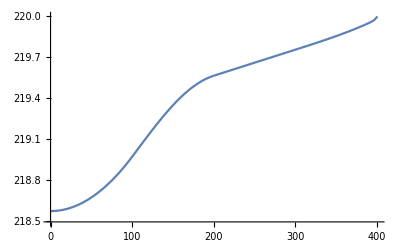

```mathematica
yy2=Table[y[i],{i,0,n}]/.ptoscrit2⟦1⟧
gg2=ListPlot[Table[{x[i],yy2⟦i+1⟧},{i,0,n}],PlotJoined->True,DisplayFunction->Identity]
```

```mathematica
valoraprox2energia =N[GGG/.ptoscrit2⟦1⟧]
```

791.805

```mathematica
valoraprox1energia
```

791.782

### Comparación de los valores obtenidos para las diferentes aproximaciones

```mathematica
TableForm[Table[{x[i],yy1⟦i+1⟧,yy2⟦i+1⟧},{i,0,n}],
TableHeadings->{None,
{"x[i] \n","y[i]  \n","y[i](trap.)\n"}}]
```

x[i] 
 | y[i]  
 | y[i](trap.)

0. | 218.575 | 218.575
4.005 | 218.575 | 218.576
8.01 | 218.577 | 218.578
12.015 | 218.58 | 218.581
16.02 | 218.585 | 218.586
20.025 | 218.591 | 218.591
24.03 | 218.598 | 218.598
28.035 | 218.606 | 218.607
32.04 | 218.616 | 218.616
36.045 | 218.626 | 218.627
40.05 | 218.639 | 218.639
44.055 | 218.652 | 218.653
48.06 | 218.667 | 218.667
52.065 | 218.683 | 218.683
56.07 | 218.7 | 218.7
60.075 | 218.718 | 218.719
64.08 | 218.738 | 218.739
68.085 | 218.759 | 218.76
72.09 | 218.781 | 218.782
76.095 | 218.805 | 218.806
80.1 | 218.83 | 218.831
84.105 | 218.856 | 218.857
88.11 | 218.884 | 218.884
92.115 | 218.912 | 218.913
96.12 | 218.942 | 218.943
100.125 | 218.974 | 218.974
104.13 | 219.006 | 219.006
108.135 | 219.038 | 219.038
112.14 | 219.07 | 219.07
116.145 | 219.101 | 219.102
120.15 | 219.133 | 219.134
124.155 | 219.164 | 219.165
128.16 | 219.195 | 219.196
132.165 | 219.225 | 219.226
136.17 | 219.255 | 219.255
140.175 | 219.283 | 219.284
144.18 | 219.311 | 219.311
148.185 | 219.338 | 219.338
152.19 | 219.363 | 219.364
156.195 | 219.388 | 219.389
160.2 | 219.412 | 219.412
164.205 | 219.434 | 219.434
168.21 | 219.455 | 219.455
172.215 | 219.474 | 219.474
176.22 | 219.492 | 219.492
180.225 | 219.508 | 219.509
184.23 | 219.523 | 219.524
188.235 | 219.536 | 219.537
192.24 | 219.548 | 219.548
196.245 | 219.558 | 219.558
200.25 | 219.567 | 219.567
204.255 | 219.574 | 219.574
208.26 | 219.582 | 219.582
212.265 | 219.589 | 219.59
216.27 | 219.597 | 219.597
220.275 | 219.605 | 219.605
224.28 | 219.612 | 219.613
228.285 | 219.62 | 219.62
232.29 | 219.628 | 219.628
236.295 | 219.635 | 219.636
240.3 | 219.643 | 219.643
244.305 | 219.651 | 219.651
248.31 | 219.658 | 219.658
252.315 | 219.666 | 219.666
256.32 | 219.673 | 219.674
260.325 | 219.681 | 219.681
264.33 | 219.689 | 219.689
268.335 | 219.696 | 219.697
272.34 | 219.704 | 219.704
276.345 | 219.712 | 219.712
280.35 | 219.719 | 219.72
284.355 | 219.727 | 219.727
288.36 | 219.735 | 219.735
292.365 | 219.742 | 219.742
296.37 | 219.75 | 219.75
300.375 | 219.757 | 219.758
304.38 | 219.765 | 219.765
308.385 | 219.773 | 219.773
312.39 | 219.78 | 219.781
316.395 | 219.788 | 219.788
320.4 | 219.796 | 219.796
324.405 | 219.804 | 219.804
328.41 | 219.812 | 219.812
332.415 | 219.82 | 219.82
336.42 | 219.828 | 219.828
340.425 | 219.836 | 219.836
344.43 | 219.844 | 219.845
348.435 | 219.853 | 219.853
352.44 | 219.861 | 219.862
356.445 | 219.87 | 219.87
360.45 | 219.879 | 219.879
364.455 | 219.888 | 219.888
368.46 | 219.898 | 219.898
372.465 | 219.907 | 219.907
376.47 | 219.917 | 219.917
380.475 | 219.927 | 219.927
384.48 | 219.937 | 219.937
388.485 | 219.948 | 219.948
392.49 | 219.959 | 219.959
396.495 | 219.972 | 219.973
400.5 | 220 | 220

#### Contraste gráfico

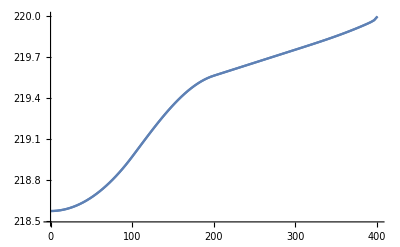

```mathematica
Show[gg1,gg2]
```

Comparamos en este gráfico las representaciones de la solución que proporciona el método de la poligonal de Euler, junto con la que se obtiene utilizando la regla de los trapecios para aproximar las integrales correspondientes.